## Recovering Evolution Sequences

```mathematica
ParallelTable[Module[{ru,ca,lt,pcas,fitness},SeedRandom[7896778+i];
Nest[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,#,(*pcas=Table[PerturbCA[{ca,ru}],Ceiling[lt/20]];*)pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1,"ReturnPerturbations"->False],Ceiling[lt/10]];
fitness=Min[Join[{lt},TestCALifeTime/@pcas]];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]],{i,5000}];
```

KernelObject::giveup: Timeout for macpro-basement.wolfram.com//usr/local/bin/wolfram 8. Received only 11 of 20 connections.

LinkObject::linkd: Unable to communicate with closed link LinkObject[ParentLink,6376,95].

LinkObject::linkn: Argument LinkObject[ParentLink,6376,95] in LinkRead[LinkObject[ParentLink,6376,95],Hold] has an invalid LinkObject number; the link may be closed.

Parallel`Developer`ConnectKernel::failinit: 1 of 195 kernels failed to initialize.

```mathematica
Select[%,#[[2]]>100&]
```

{{{268421576596783154125046530204266236812,4,1},111},{{147403944448280291853900806387327553596,4,1},107},{{248165598297832837437916710957193630216,4,1},104},{{134352701883209903342527245958435650060,4,1},102},{{288096107223535296419424673988897412364,4,1},106},{{339118334212898847537752633217327057976,4,1},109},{{321033973632549904983932956520209330696,4,1},101},{{105095753086267005525767099158674078604,4,1},106},{{267017653732987573795364345207890141512,4,1},103},{{110572144621941770841649306920052872204,4,1},104},{{285844326421166081060892845611091535884,4,1},111},{{76459985983155900365494599730072701452,4,1},101},{{287426194400923611234870030427559824140,4,1},103},{{328091281327807596318497304928484883976,4,1},102},{{119036002119603607356514909757868286216,4,1},102},{{317299368495465910304892902399080254264,4,1},107},{{278045845346607563032787258414437791544,4,1},101},{{117583592864712737061416347667069988156,4,1},101},{{4805101858768707264031667489079952184,4,1},108},{{7977385475371059556823827836905458188,4,1},102},{{28822720352419846592599677408367493436,4,1},101},{{46058842733434566198293092266537120384,4,1},101},{{299459058088077823758143088095350287424,4,1},101},{{140760482982177850157208130958283113584,4,1},104},{{68344969204256202378277879430275436104,4,1},102},{{25359040487030105047738027699989445448,4,1},124},{{50384664521204969494536571058688395144,4,1},101},{{275829246158421973968735855928619872784,4,1},104},{{187801454374097774235135078616998547980,4,1},102},{{94341792732834871885391301103528730764,4,1},118},{{123547048548354375987206496656127777288,4,1},104},{{145847175969039188329249499360869168136,4,1},101},{{50742575811329985903162916962404076296,4,1},112},{{17236508088123058982014956771682294592,4,1},103},{{44467251686122792070513828103482331660,4,1},105},{{179559826355654686003966918665743860592,4,1},107},{{66958958108797332090631032629696739612,4,1},109}}

```mathematica
Select[%119,#[[2]]>100&->"Index"]
```

{17,29,240,264,352,417,444,885,1123,1214,1537,1666,1679,1726,2423,2445,2505,2525,2529,2578,2737,2774,2845,3212,3497,3624,3800,3830,3925,4038,4060,4143,4668,4714,4838,4896,4906}

#### THIS FOR ALL:

```mathematica
Select[%119,#[[2]]>100&->{"Index","Element"}]
```

<|Element→{{{268421576596783154125046530204266236812,4,1},111},{{147403944448280291853900806387327553596,4,1},107},{{248165598297832837437916710957193630216,4,1},104},{{134352701883209903342527245958435650060,4,1},102},{{288096107223535296419424673988897412364,4,1},106},{{339118334212898847537752633217327057976,4,1},109},{{321033973632549904983932956520209330696,4,1},101},{{105095753086267005525767099158674078604,4,1},106},{{267017653732987573795364345207890141512,4,1},103},{{110572144621941770841649306920052872204,4,1},104},{{285844326421166081060892845611091535884,4,1},111},{{76459985983155900365494599730072701452,4,1},101},{{287426194400923611234870030427559824140,4,1},103},{{328091281327807596318497304928484883976,4,1},102},{{119036002119603607356514909757868286216,4,1},102},{{317299368495465910304892902399080254264,4,1},107},{{278045845346607563032787258414437791544,4,1},101},{{117583592864712737061416347667069988156,4,1},101},{{4805101858768707264031667489079952184,4,1},108},{{7977385475371059556823827836905458188,4,1},102},{{28822720352419846592599677408367493436,4,1},101},{{46058842733434566198293092266537120384,4,1},101},{{299459058088077823758143088095350287424,4,1},101},{{140760482982177850157208130958283113584,4,1},104},{{68344969204256202378277879430275436104,4,1},102},{{25359040487030105047738027699989445448,4,1},124},{{50384664521204969494536571058688395144,4,1},101},{{275829246158421973968735855928619872784,4,1},104},{{187801454374097774235135078616998547980,4,1},102},{{94341792732834871885391301103528730764,4,1},118},{{123547048548354375987206496656127777288,4,1},104},{{145847175969039188329249499360869168136,4,1},101},{{50742575811329985903162916962404076296,4,1},112},{{17236508088123058982014956771682294592,4,1},103},{{44467251686122792070513828103482331660,4,1},105},{{179559826355654686003966918665743860592,4,1},107},{{66958958108797332090631032629696739612,4,1},109}},Index→{17,29,240,264,352,417,444,885,1123,1214,1537,1666,1679,1726,2423,2445,2505,2525,2529,2578,2737,2774,2845,3212,3497,3624,3800,3830,3925,4038,4060,4143,4668,4714,4838,4896,4906}|>

```mathematica
NotebookSave[]
```

```mathematica
Now
```

Thu 23 Jan 2025 02:57:57GMT-5

```mathematica
ParallelTable[Module[{ru,ca,lt,pcas,fitness},SeedRandom[7726778+i];
Nest[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,#,(*pcas=Table[PerturbCA[{ca,ru}],Ceiling[lt/20]];*)pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1,"ReturnPerturbations"->False],Ceiling[lt/10]];
fitness=Min[Join[{lt},TestCALifeTime/@pcas]];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]],{i,5000}];
```

```mathematica
Select[%,#[[2]]>100&]
```

{{{249655052911842972503105465786245423372,4,1},101},{{179079137400185473786391819702541282316,4,1},111},{{227300279103717937375901636324241679928,4,1},103},{{279170265771946658655474501222538692492,4,1},114},{{113554917644982243172837530688048101952,4,1},103},{{252507139021300249072588345221334974732,4,1},107},{{2008950354646838645508008819751683724,4,1},101},{{226015304160762721737655680886414531328,4,1},101},{{144145145453709280215486890041407760140,4,1},106},{{323346474827969055007794639890839674892,4,1},108},{{321706856175457720374293484094457248312,4,1},102},{{82621004647145585070973878096678172544,4,1},102},{{158194304512403226430615670631995011596,4,1},101},{{74854193573603039495257316762623916812,4,1},101},{{195424492496079767509053018893716980764,4,1},101},{{265071312472082352533487301754498275896,4,1},103},{{267982875530361130482203677471860893056,4,1},107},{{202325941907635500453679147036727315328,4,1},104},{{297274882967345950128571968445382186124,4,1},104},{{268526035006191993717616300354348003848,4,1},104},{{90301383028378803733740017346685657096,4,1},102},{{272480688721516524826602064283746072588,4,1},123},{{67706710625287194458561323099266580620,4,1},106},{{122756841542307176723461821055157943432,4,1},102},{{218912643215463401112202604742041986560,4,1},109},{{73048792447863257076349756348476938808,4,1},106},{{30116018899564803694319991112919091080,4,1},104},{{313250599264395119456857147759593994508,4,1},108},{{31454797907058801713769223942564501248,4,1},113},{{253111851654989821263342165042836021516,4,1},103},{{1888156755161854070810212381741134736,4,1},101},{{249040412549299144651908129003625461904,4,1},101},{{29710399076215276059739093407009123896,4,1},109},{{128036231242624368420673617689650707248,4,1},106},{{133104829459696075040951708854672090640,4,1},116}}

```mathematica
Select[,#[[2]]>100&->{"Index","Element"}]
```

<|Element→{{{249655052911842972503105465786245423372,4,1},101},{{179079137400185473786391819702541282316,4,1},111},{{227300279103717937375901636324241679928,4,1},103},{{279170265771946658655474501222538692492,4,1},114},{{113554917644982243172837530688048101952,4,1},103},{{252507139021300249072588345221334974732,4,1},107},{{2008950354646838645508008819751683724,4,1},101},{{226015304160762721737655680886414531328,4,1},101},{{144145145453709280215486890041407760140,4,1},106},{{323346474827969055007794639890839674892,4,1},108},{{321706856175457720374293484094457248312,4,1},102},{{82621004647145585070973878096678172544,4,1},102},{{158194304512403226430615670631995011596,4,1},101},{{74854193573603039495257316762623916812,4,1},101},{{195424492496079767509053018893716980764,4,1},101},{{265071312472082352533487301754498275896,4,1},103},{{267982875530361130482203677471860893056,4,1},107},{{202325941907635500453679147036727315328,4,1},104},{{297274882967345950128571968445382186124,4,1},104},{{268526035006191993717616300354348003848,4,1},104},{{90301383028378803733740017346685657096,4,1},102},{{272480688721516524826602064283746072588,4,1},123},{{67706710625287194458561323099266580620,4,1},106},{{122756841542307176723461821055157943432,4,1},102},{{218912643215463401112202604742041986560,4,1},109},{{73048792447863257076349756348476938808,4,1},106},{{30116018899564803694319991112919091080,4,1},104},{{313250599264395119456857147759593994508,4,1},108},{{31454797907058801713769223942564501248,4,1},113},{{253111851654989821263342165042836021516,4,1},103},{{1888156755161854070810212381741134736,4,1},101},{{249040412549299144651908129003625461904,4,1},101},{{29710399076215276059739093407009123896,4,1},109},{{128036231242624368420673617689650707248,4,1},106},{{133104829459696075040951708854672090640,4,1},116}},Index→{51,183,255,412,490,835,917,984,1029,1233,1515,1767,1786,2120,2167,2243,2258,2302,2410,2424,2475,2526,2587,2591,2626,2758,2941,3198,3265,4147,4209,4311,4664,4697,4963}|>

```mathematica
NotebookSave[]
```

```mathematica
Now
```

Thu 23 Jan 2025 03:05:04GMT-5

```mathematica
ParallelTable[Module[{ru,ca,lt,pcas,fitness},SeedRandom[9896778+i];
Nest[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,#,(*pcas=Table[PerturbCA[{ca,ru}],Ceiling[lt/20]];*)pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1,"ReturnPerturbations"->False],Ceiling[lt/10]];
fitness=Min[Join[{lt},TestCALifeTime/@pcas]];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]],{i,10000}];
```

```mathematica
Select[%,#[[2]]>100&]
```

{{{329544069266708592463225775856558462236,4,1},105},{{123508487018209309850362627631298163528,4,1},110},{{163313090342284595938913846502066693128,4,1},112},{{322945229948492362661182721894198120504,4,1},101},{{292198784645215941321088592407235122960,4,1},101},{{31695255581700470911902716317105858104,4,1},105},{{4276479724016731948913745978675710344,4,1},104},{{234969409870737885186155122705247389456,4,1},106},{{305594030182245330593005536812098379020,4,1},136},{{86864532868683262332171869371746211656,4,1},107},{{313404655246606715143923602520383021628,4,1},107},{{206520768166068154372125868922628220680,4,1},101},{{275427862818522291843761996681464259136,4,1},101},{{241518285231888740052080333575106094856,4,1},101},{{265649783286254331336047586327636247424,4,1},108},{{84478019421191510670475347975090695304,4,1},102},{{323972994405677581261299364309982822984,4,1},101},{{139388508222756839705700366249736547080,4,1},101},{{69595485954279110481952373371706328460,4,1},112},{{152887335389782929274275445853437581964,4,1},104},{{214182135155451017991276257555564800,4,1},113},{{276033802575773574714948886195065539400,4,1},112},{{323956930294760472040543117745573889864,4,1},104},{{110015945415894856459943883956706106928,4,1},103},{{100781445248190497550915302640180589452,4,1},106},{{34074507461861229215498324156407553288,4,1},103},{{26271098448565414638434966462483153548,4,1},104},{{323225562089687832334207018339055681288,4,1},104},{{284557779697216700155468611559049810816,4,1},102},{{136387264312167251298710646813606853644,4,1},110},{{333412730384010924473712496196989406776,4,1},115},{{177672575103988063392759613333409631116,4,1},106},{{234876938465135365439119040628466918984,4,1},108},{{139711864353953990056336175208405135112,4,1},102},{{85123320662285613542598906103675541900,4,1},104},{{43999191294040384362868476713575917896,4,1},106},{{62334676211067655056444864681450042896,4,1},103},{{250537532966085524803188231638477559304,4,1},103},{{155126299774036898109282870901130767160,4,1},106},{{172585717296189517156735203671700137500,4,1},102},{{3119893522619878841243738862909089292,4,1},101},{{322124877738225522656378403894004819724,4,1},110},{{280861221592569736193855132280195746312,4,1},103},{{274497712902856292362158459547678821660,4,1},102},{{313795251506533548422834534527130163852,4,1},111},{{50758326146301751784736482597649065032,4,1},108},{{266515228004501182380072598634386380296,4,1},101},{{282351796037962970657007342130741841472,4,1},102},{{58660367730971486367777885061724439184,4,1},104},{{246542310115611634618827656617722701632,4,1},104},{{107447355040682041878315967596949087056,4,1},101},{{172641118172523465139163397901285743628,4,1},102},{{88748899626595012307086691574190809660,4,1},105},{{327704894924594339287485143965479296312,4,1},109},{{195461560254987692902190917543593873208,4,1},105},{{82573654432052839615243008188031401992,4,1},101},{{232291912060393373038155881533940211520,4,1},113},{{237704553255020977898718559585218821128,4,1},102},{{68921575965966799467835064231816027656,4,1},102},{{24756839899959706319040451428922970376,4,1},108},{{289364171492315924137486550507194162056,4,1},117},{{196707122929992662394501893164151263120,4,1},103},{{316080973066541245194327095335075455792,4,1},105},{{227135195378627184969662599411794102848,4,1},102},{{186283904168272826496927796595897279032,4,1},115},{{76959122483754835606158870556013617480,4,1},104},{{40266955896376127002408125426774126352,4,1},101},{{309724267472797781878974169522980045192,4,1},102},{{197984107404214585988723854963415490368,4,1},106},{{107916005792094408002911209179238419328,4,1},103},{{105883381022833302762043779199245117496,4,1},101},{{174624983285913979400305481159641858872,4,1},103}}

```mathematica
Select[,#[[2]]>100&->{"Index","Element"}]
```

<|Element→{{{329544069266708592463225775856558462236,4,1},105},{{123508487018209309850362627631298163528,4,1},110},{{163313090342284595938913846502066693128,4,1},112},{{322945229948492362661182721894198120504,4,1},101},{{292198784645215941321088592407235122960,4,1},101},{{31695255581700470911902716317105858104,4,1},105},{{4276479724016731948913745978675710344,4,1},104},{{234969409870737885186155122705247389456,4,1},106},{{305594030182245330593005536812098379020,4,1},136},{{86864532868683262332171869371746211656,4,1},107},{{313404655246606715143923602520383021628,4,1},107},{{206520768166068154372125868922628220680,4,1},101},{{275427862818522291843761996681464259136,4,1},101},{{241518285231888740052080333575106094856,4,1},101},{{265649783286254331336047586327636247424,4,1},108},{{84478019421191510670475347975090695304,4,1},102},{{323972994405677581261299364309982822984,4,1},101},{{139388508222756839705700366249736547080,4,1},101},{{69595485954279110481952373371706328460,4,1},112},{{152887335389782929274275445853437581964,4,1},104},{{214182135155451017991276257555564800,4,1},113},{{276033802575773574714948886195065539400,4,1},112},{{323956930294760472040543117745573889864,4,1},104},{{110015945415894856459943883956706106928,4,1},103},{{100781445248190497550915302640180589452,4,1},106},{{34074507461861229215498324156407553288,4,1},103},{{26271098448565414638434966462483153548,4,1},104},{{323225562089687832334207018339055681288,4,1},104},{{284557779697216700155468611559049810816,4,1},102},{{136387264312167251298710646813606853644,4,1},110},{{333412730384010924473712496196989406776,4,1},115},{{177672575103988063392759613333409631116,4,1},106},{{234876938465135365439119040628466918984,4,1},108},{{139711864353953990056336175208405135112,4,1},102},{{85123320662285613542598906103675541900,4,1},104},{{43999191294040384362868476713575917896,4,1},106},{{62334676211067655056444864681450042896,4,1},103},{{250537532966085524803188231638477559304,4,1},103},{{155126299774036898109282870901130767160,4,1},106},{{172585717296189517156735203671700137500,4,1},102},{{3119893522619878841243738862909089292,4,1},101},{{322124877738225522656378403894004819724,4,1},110},{{280861221592569736193855132280195746312,4,1},103},{{274497712902856292362158459547678821660,4,1},102},{{313795251506533548422834534527130163852,4,1},111},{{50758326146301751784736482597649065032,4,1},108},{{266515228004501182380072598634386380296,4,1},101},{{282351796037962970657007342130741841472,4,1},102},{{58660367730971486367777885061724439184,4,1},104},{{246542310115611634618827656617722701632,4,1},104},{{107447355040682041878315967596949087056,4,1},101},{{172641118172523465139163397901285743628,4,1},102},{{88748899626595012307086691574190809660,4,1},105},{{327704894924594339287485143965479296312,4,1},109},{{195461560254987692902190917543593873208,4,1},105},{{82573654432052839615243008188031401992,4,1},101},{{232291912060393373038155881533940211520,4,1},113},{{237704553255020977898718559585218821128,4,1},102},{{68921575965966799467835064231816027656,4,1},102},{{24756839899959706319040451428922970376,4,1},108},{{289364171492315924137486550507194162056,4,1},117},{{196707122929992662394501893164151263120,4,1},103},{{316080973066541245194327095335075455792,4,1},105},{{227135195378627184969662599411794102848,4,1},102},{{186283904168272826496927796595897279032,4,1},115},{{76959122483754835606158870556013617480,4,1},104},{{40266955896376127002408125426774126352,4,1},101},{{309724267472797781878974169522980045192,4,1},102},{{197984107404214585988723854963415490368,4,1},106},{{107916005792094408002911209179238419328,4,1},103},{{105883381022833302762043779199245117496,4,1},101},{{174624983285913979400305481159641858872,4,1},103}},Index→{93,173,212,419,471,626,760,964,1059,1155,1250,1289,1299,1844,1952,2139,2208,2220,2350,2459,2602,2710,2714,3035,3215,3314,3395,3512,3806,3880,3888,3947,3958,4672,4707,4779,4863,4961,5049,5315,5322,5351,5359,5451,5524,5651,5676,5706,5884,6206,6224,6353,6360,6851,7164,7203,7367,7695,7779,7834,8072,8174,8673,8988,9001,9107,9246,9381,9395,9407,9585,9826}|>

```mathematica
NotebookSave[]
```

```mathematica
Now
```

Thu 23 Jan 2025 03:16:52GMT-5

## Treatment from Symptoms

```mathematica
awh = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},(If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ allperts[ru, init, txspec])];
```

```mathematica
awh
```

```mathematica
awh[[3]]
```

{1,3,2,3,4,3,4,4,4,6,7,8,9,10,9,9,10,11,10,8,9,9,11,12,12,13,11,8,9,8,8,9,10,10,11,13,13,14,15,14,15,9,9,10,12,12,14,15,15,14,15,16,18,18,20,21,21,20,20,19,20,21,22,22,23,24,24,25,26,26,27,28,27,26,25,23,23,24,25,25,26,27,26,26,27,28,27,26,25,24,10,9,8,7,6,5,4,3,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
rh = Module[
{ru = {299459058088077823758143088095350287424,4,1},
init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
SeedRandom[444666];
ParallelMap[HealCA[ru, init, txspec, #, 1, #==101&, "Order"->"Random"]&,Select[allperts[ru, init, txspec], Keys[#][[1, 1]]<=50&]]];
```

```mathematica
rh
```

```mathematica
treatsteps=If[Length[#]==0,Missing[],Keys[#][[1,1,1]]]&/@rh
```

{Missing[],Missing[],77,Missing[],73,Missing[],Missing[],3,3,Missing[],3,61,66,5,5,62,16,40,Missing[],Missing[],18,6,79,42,Missing[],Missing[],Missing[],63,10,Missing[],6,10,6,Missing[],54,Missing[],Missing[],Missing[],62,6,Missing[],75,Missing[],52,70,Missing[],Missing[],58,18,12,Missing[],Missing[],Missing[],Missing[],24,Missing[],8,Missing[],60,32,33,8,39,17,9,47,Missing[],Missing[],72,58,17,69,22,27,Missing[],Missing[],54,Missing[],30,Missing[],47,Missing[],35,67,Missing[],Missing[],Missing[],39,72,Missing[],Missing[],Missing[],35,35,Missing[],11,53,16,52,Missing[],Missing[],Missing[],Missing[],33,18,63,52,35,36,13,42,38,87,29,20,16,Missing[],16,16,29,Missing[],Missing[],32,48,55,Missing[],Missing[],13,13,31,16,19,13,14,Missing[],74,72,66,16,16,16,13,Missing[],17,67,Missing[],57,Missing[],Missing[],15,31,41,27,Missing[],14,66,78,15,23,14,24,Missing[],16,73,63,75,Missing[],16,21,Missing[],Missing[],76,17,17,58,65,39,32,83,16,Missing[],15,48,Missing[],Missing[],15,17,16,Missing[],Missing[],Missing[],Missing[],37,15,36,23,19,Missing[],Missing[],71,60,70,50,39,57,66,51,31,61,37,59,70,16,Missing[],16,Missing[],51,Missing[],Missing[],16,16,26,Missing[],18,Missing[],72,61,66,68,66,24,56,61,34,30,18,52,32,52,68,27,Missing[],53,17,Missing[],Missing[],Missing[],Missing[],Missing[],38,Missing[],75,28,29,79,22,23,80,66,69,Missing[],31,65,69,31,18,31,43,34,45,Missing[],23,Missing[],37,69,30,63,53,76,49,Missing[],28,27,27,72,23,21,72,68,65,74,30,55,55,51,64,50,76,60,Missing[],21,19,Missing[],56,61,19,48,Missing[],19,26,29,49,48,72,47,38,49,29,21,45,45,41,52,54,31,38,33,54,41,60,26,Missing[],Missing[],38,38,29,48,26,40,48,42,47,38,53,53,57,46,26,Missing[],20,25,23,20,38,30,22,79,22,45,39,30,52,41,48,50,Missing[],21,21,60,22,30,Missing[],52,63,60,36,46,Missing[],33,63,61,Missing[],41,31,Missing[],38,63,26,22,51,67,22,Missing[],Missing[],66,Missing[],56,44,63,Missing[],44,56,23,23,35,25,57,58,35,34,38,23,47,23,51,49,27,27,37,Missing[],66,24,Missing[],82,68,31,23,55,65,41,39,64,28,32,26,24,71,73,71,25,39,67,24,76,37,Missing[],35,76,87,42,65,38,54,68,66,65,41,78,Missing[],Missing[],61,78,46,Missing[],60,47,51,25,28,31,55,31,39,41,25,72,57,49,42,39,Missing[],40,Missing[],55,28,30,39,66,39,68,70,56,44,Missing[],33,66,66,85,39,89,26,45,26,63,60,68,29,31,36,31,38,69,26,26,42,63,85,79,74,32,27,32,28,49,39,26,Missing[],49,66,70,30,36,26,39,72,Missing[],58,87,72,33,44,88,59,30,86,59,52,29,71,35,32,88,39,51,39,71,31,28,78,Missing[],27,28,52,47,36,Missing[],64,33,49,48,39,63,Missing[],56,78,Missing[],28,90,Missing[],28,52,29,Missing[],37,39,79,45,44,39,60,58,Missing[],62,46,39,39,36,Missing[],Missing[],41,87,39,66,58,73,31,92,30,64,Missing[],33,35,35,59,76,86,38,62,67,64,37,68,36,36,31,56,Missing[],72,69,61,41,65,62,69,69,Missing[],Missing[],36,52,50,45,70,34,39,64,39,79,32,42,61,50,30,45,33,59,90,30,45,30,57,47,52,67,75,62,Missing[],Missing[],33,69,44,36,71,66,66,Missing[],46,65,50,39,64,31,31,35,66,78,60,42,60,52,37,70,60,74,33,56,32,84,32,67,33,38,58,59,64,39,44,77,45,62,71,64,60,57,38,48,37,Missing[],39,86,45,53,66,34,59,51,63,76,55,60,44,35,52,64,51,58,71,66,48,53,53,64,52,66,75,36,42,64,55,58,60,78,57,65,39,60,68,52,57,51,34,39,39,52,58,72,42,59,81,70,56,70,37,48,59,39,68,70,70,55,35,54,53,59,37,58,Missing[],47,59,39,38,52,60,39,55,40,56,37,50,51,36,66,74,79,57,39,48,70,63,65,58,45,57,52,63,55,Missing[],59,55,43,65,36,43,46,66,40,Missing[],36,48,39,38,66,71,37,81,37,37,39,60,61,72,71,73,74,47,58,72,63,73,66,54,48,37,54,54,Missing[],56,41,47,42,41,74,48,66,41,40,64,65,84,48,52,38,38,45,43,53,39,41,72,46,53,78,75,55,60,44,60,49,51,38,Missing[],58,52,66,41,84,73,70,77,62,38,57,56,83,48,65,72,85,44,63,56,66,58,39,39,54,64,52,47,74,67,57,44,54,80,75,48,39,50,87,56,39,72,77,86,39,57,58,59,68,39,52,62,64,46,77,39,75,65,88,43,58,54,42,59,89,64,62,44,42,43,59,42,72,72,78,73,75,43,85,49,54,62,43,40,82,57,60,61,59,60,41,77,59,61,77,63,66,64,91,84,60,82,97,87,67,78,65,43,41,42,88,49,63,41,66,41,41,66,47,69,41,60,73,58,58,Missing[],62,49,75,85,41,78,82,56,50,80,41,56,54,64,66,56,58,45,51,64,79,42,59,88,69,56,90,42,60,42,63,42,42,59,43,60,56,50,60,88,86,83,71,65,59,43,50,63,Missing[],48,42,52,65,63,77,54,57,85,68,55,49,55,72,43,50,68,78,63,77,52,73,62,Missing[],65,56,69,60,71,62,56,46,45,60,49,69,72,47,73,58,77,67,57,86,52,85,50,45,68,60,46,71,50,53,89,51,85,45,59,46,45,44,83,56,53,57,52,86,50,Missing[],75,Missing[],46,47,61,63,57,57,72,89,45,70,47,63,67,51,59,64,83,46,59,65,68,67,56,70,81,65,60,68,66,65,48,52,68,62,69,62,50,49,56,57,49,54,68,63,79,75,85,71,79,56,72,51,57,47,74,62,51,77,75,53,52,81,80,54,63,56,Missing[],47,65,49,82,79,55,68,60,85,65,75,83,50,63,49,83,77,57,89,72,89,82,68,57,47,67,58,61,54,67,48,52,53,72,70,53,56,82,85,69,62,52,56,49,67,84,72,60,55,78,51,56,57,70,57,61,64,53,68,75,68,56,84,86,63,68,63,49,73,65,65,50,51,48,74,63,58,70,70,64,68,52,67,82,75,76,63,63,71,68,54,55,49,67,82,60,89,53,81,50,51,69,70,66,54,67,57,87,50,63,66,51,53,52,68,71,70,66,59,86,54,73,79,70,82,60,56,52,72,65,51,58,65,52,53,69,87,51,74,51,55,50,85,71,58,78,51,90,57,67,67,54,62,58,63,60,78,59,52,74,68,55,51,50,76,61,55,60,52,79,51,70,75,66,51,66,60,57,72,68,62,62,73,52,79,66,51,65,62,60,86,58,52,73,51,72,67,67,57,66,51,59,61,61,73,63}

```mathematica
Length[awh[[All,25]]]
```

4383

```mathematica
Length[]
```

1410

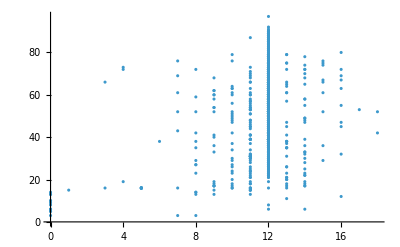

```mathematica
ListPlot[Transpose[{awh[[;;1410,25]],}]]
```

```mathematica
awh50 = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},(If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ Select[allperts[ru, init, txspec], Keys[#][[1, 1]]<=50&])];
```

```mathematica
MapThread[Rule,{awh50,rh}]
```

```mathematica
Length/@awh50
```

{201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201,201}

```mathematica
Length[rh]
```

1410

```mathematica
Length[awh]
```

4383

```mathematica
alltrain =Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
MapThread[If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #1, "ReturnPerturbations"->False]->Keys[#2][[1, 1]]&, {Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], Catenate[rh]}]];
```

### Width History Prognosis

```mathematica
Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {25, {-110, 110}}, aps, pca, ca},((If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False])->TestCALifeTime[PerturbedCellularAutomaton[ru, init, {400,{-110,110}}, #]])&/@ allperts[ru, init, txspec]]
```

```mathematica
pd[First[#]]&/@traindata[[outs]]
```

PredictorFunction::mlincfttp: Incompatible variable type (Boolean) and variable value (3).

{17.1874,PredictorFunction[…][{1,3,2,3,4,3,4,4,4,6,7,8,9,10,9,9,10,11,10,8,9,9,11,12,12,13}],17.743,17.743,63.0881,17.743,78.2301,84.9909,20.7683,17.743,103.673,80.5617,22.142,19.2527,24.226,79.0121,20.7683,78.0777,87.8383,33.1947,21.1902,85.9876,78.3499,109.735,72.375,21.5841,22.142,97.7561,31.2513,93.7914,27.3524,21.5841,93.7914,98.5614,83.3126,73.278,27.3524,34.1159,107.392,70.4069,107.392,57.2234,91.5424,92.4617,82.0392,57.7002,96.2515,107.392,109.924,107.392,71.835,60.2071,59.0074,34.1159,27.7415,107.392,101.039,107.136,28.3474,62.8625,32.1055,84.8554,40.874,40.874,40.874,29.7496,77.9275,70.0569,34.1215,83.9491,87.3986,38.2379,74.8757,28.3474,28.3474,35.7541,74.4148,62.8625,37.4303,65.3118,39.7902,86.743,62.0479,77.9234,37.0859,71.5206,108.048,85.8735,71.9575,66.106,28.3474,39.8003,62.8625,54.5307,65.3118,86.743,71.008,86.743,61.6018,69.579,93.1873,85.8735,70.3293,74.9027,65.2752,85.8735,65.3118,73.8729,39.8003,86.4816,71.8788,97.6228,65.2752,62.4567,71.6886,66.6829,65.3118,60.6419,69.0939,85.8735,79.4017,86.4816,73.2564,68.8522,109.924,97.6228,97.6228,79.8851,60.5924,60.8237,79.4017,73.033,60.6419,86.8442,80.2134,109.924,109.924,104.239,60.5157,79.5802,65.4799,65.3118,65.3118,79.4017,69.0939,59.8127,66.2917,80.9274,87.3522,79.0878,67.2934,64.6506,76.4702,66.0268,86.8442,78.5725,85.8735,85.3316,86.8442,85.3316,79.5158,79.5158,83.6056,80.9274,79.1402,76.9535,87.3522,109.924,86.4816,70.9067,64.7649,85.3316,86.8442,85.8735,84.7903,85.8735,85.8735,85.8735,85.3316,85.8735,79.5158,79.5158,85.3316,80.3315,66.0094,69.8205,79.4017,86.8442,65.3118,84.7903,85.8735,85.8735,84.7903,85.8735,85.8735,85.8735,85.8735,85.3316,85.8735,79.5158,69.8205,65.3118,86.8442,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.3316,78.5725,65.8537,80.3855,65.3118,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,65.3118,80.3855,85.8735,85.3316,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.3316,85.8735,80.9274,86.8442,86.8442,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.8735,85.3316}

```mathematica
pd
```

PredictorFunction[…]

```mathematica
traindata[[outs]]
```

## Clustering Trees

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]]];
```

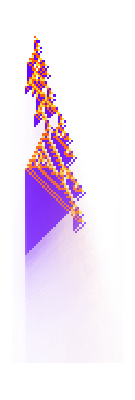

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[pcas,{3,1,2}],{2}]]
```

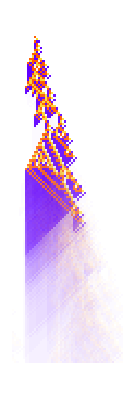

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[RandomSample[pcas,50],{3,1,2}],{2}]]
```

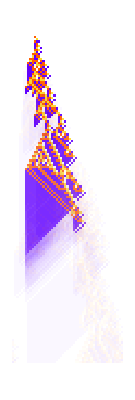

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[RandomSample[pcas,30],{3,1,2}],{2}]]
```

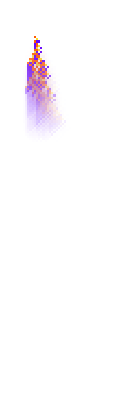

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[Select[pcas,0<TestCALifeTime[#]<50&],{3,1,2}],{2}]]
```

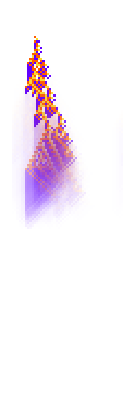

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[Select[pcas,70<TestCALifeTime[#]<90&],{3,1,2}],{2}]]
```

```mathematica
FindClusters[pcas,5]
```

$Aborted

```mathematica
FindClusters[RandomSample[pcas,200],5]
```

```mathematica
Length[%]
```

5

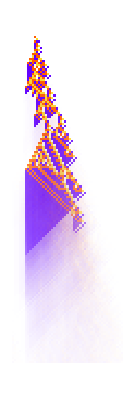
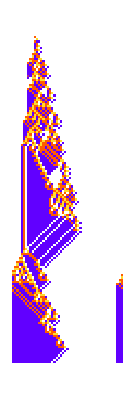
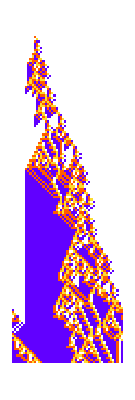
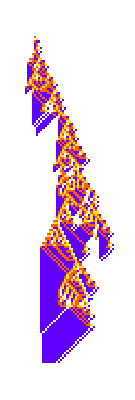
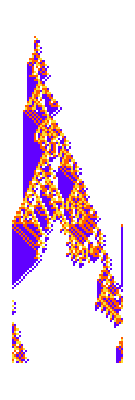

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[#,{3,1,2}],{2}]]&/@
```

```mathematica
Length/@
```

{195,2,1,1,1}

## Genetic Diversity

```mathematica
quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{{1711981961654267314772700605740280896,4,1},{1711987032256668227690306592553102400,4,1},{1711992102859069140607912579365923904,4,1},{1711997173461470053525518566178745408,4,1},{22979629894212921281233613570225794112,4,1},{22979634964815322194151219557038615616,4,1},{22979640035417723107068825543851437120,4,1},{22979645106020124019986431530664258624,4,1},{44247277826771575247694526534711307328,4,1},{44247282897373976160612132521524128832,4,1},{44247287967976377073529738508336950336,4,1},{44247293038578777986447344495149771840,4,1},{65514925759330229214155439499196820544,4,1},{65514930829932630127073045486009642048,4,1},{65514935900535031039990651472822463552,4,1},{65514940971137431952908257459635285056,4,1},{86782573691888883180616352463682333760,4,1},{86782578762491284093533958450495155264,4,1},{86782583833093685006451564437307976768,4,1},{86782588903696085919369170424120798272,4,1},{108050221624447537147077265428167846976,4,1},{108050226695049938059994871414980668480,4,1},{108050231765652338972912477401793489984,4,1},{108050236836254739885830083388606311488,4,1},{129317869557006191113538178392653360192,4,1},{129317874627608592026455784379466181696,4,1},{129317879698210992939373390366279003200,4,1},{129317884768813393852290996353091824704,4,1},{150585517489564845079999091357138873408,4,1},{150585522560167245992916697343951694912,4,1},{150585527630769646905834303330764516416,4,1},{150585532701372047818751909317577337920,4,1},{171853165422123499046460004321624386624,4,1},{171853170492725899959377610308437208128,4,1},{171853175563328300872295216295250029632,4,1},{171853180633930701785212822282062851136,4,1},{193120813354682153012920917286109899840,4,1},{193120818425284553925838523272922721344,4,1},{193120823495886954838756129259735542848,4,1},{193120828566489355751673735246548364352,4,1},{214388461287240806979381830250595413056,4,1},{214388466357843207892299436237408234560,4,1},{214388471428445608805217042224221056064,4,1},{214388476499048009718134648211033877568,4,1},{235656109219799460945842743215080926272,4,1},{235656114290401861858760349201893747776,4,1},{235656119361004262771677955188706569280,4,1},{235656124431606663684595561175519390784,4,1},{256923757152358114912303656179566439488,4,1},{256923762222960515825221262166379260992,4,1},{256923767293562916738138868153192082496,4,1},{256923772364165317651056474140004904000,4,1},{278191405084916768878764569144051952704,4,1},{278191410155519169791682175130864774208,4,1},{278191415226121570704599781117677595712,4,1},{278191420296723971617517387104490417216,4,1},{299459053017475422845225482108537465920,4,1},{299459058088077823758143088095350287424,4,1},{299459063158680224671060694082163108928,4,1},{299459068229282625583978300068975930432,4,1},{320726700950034076811686395073022979136,4,1},{320726706020636477724604001059835800640,4,1},{320726711091238878637521607046648622144,4,1},{320726716161841279550439213033461443648,4,1}}

```mathematica
Position[%,{299459058088077823758143088095350287424,4,1}]
```

{{58}}

```mathematica
PlotCA[]
```

```mathematica
PlotCA[PerturbedCellularAutomaton[{171853175563328300872295216295250029632,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,450},Mesh->True]
```

-Graphics-

```mathematica
PerturbedCellularAutomaton[{171853175563328300872295216295250029632,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>][[1,25]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,2,1,2,1,2,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

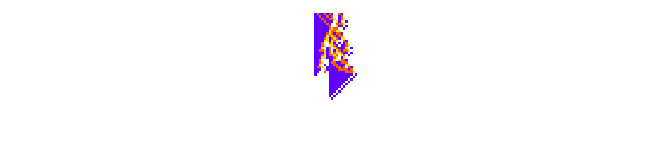

```mathematica
ArrayPlot[CellularAutomaton[{171853175563328300872295216295250029632,4,1},,50],ColorRules->colorrules]
```

```mathematica
PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>][[1,25]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,2,1,2,1,2,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

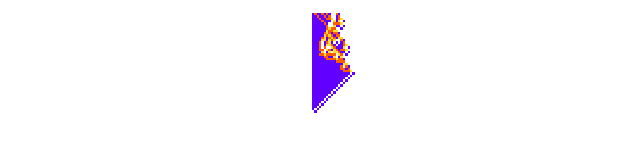

```mathematica
ArrayPlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1},,50],ColorRules->colorrules]
```

```mathematica
PerturbedCellularAutomaton[{171853175563328300872295216295250029632,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>]-PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>]
```

```mathematica
ArrayPlot[First[]]
```

-Graphics-

```mathematica
Position[First[],Except[0],{2},Heads->False]
```

{{37,112},{38,111},{38,112},{39,110},{39,112},{39,113},{40,109},{40,111},{40,112},{40,113},{40,114},{41,112},{41,113},{41,114},{41,115},{42,111},{42,112},{42,115},{43,110},{43,111},{43,112},{43,113},{43,115},{44,109},{44,110},{44,111},{44,112},{44,113},{44,114},{44,115},{44,116},{45,109},{45,110},{45,111},{45,112},{45,114},{45,115},{45,117},{46,109},{46,110},{46,112},{46,115},{46,116},{47,108},{47,109},{47,110},{47,111},{47,116},{47,117},{48,110},{48,111},{48,117},{48,118},{49,109},{49,110},{49,111},{49,112},{50,108},{50,109},{50,110},{50,111},{50,112},{51,107},{51,108},{51,109},{51,110},{51,111},{51,112},{52,107},{52,108},{52,109},{52,110},{52,111},{52,112},{53,107},{53,108},{53,109},{53,110},{53,111},{53,112},{54,107},{54,108},{54,109},{54,110},{54,111},{54,112},{55,107},{55,108},{55,109},{55,110},{55,111},{55,112},{56,107},{56,108},{56,109},{56,110},{56,111},{56,112},{57,107},{57,108},{57,109},{57,110},{57,111},{57,112},{58,107},{58,108},{58,109},{58,110},{58,111},{58,112},{59,107},{59,108},{59,109},{59,110},{59,111},{59,112},{60,107},{60,108},{60,109},{60,110},{60,111},{60,112},{61,107},{61,108},{61,109},{61,110},{61,111},{61,113},{62,107},{62,108},{62,109},{62,110},{62,112},{63,107},{63,108},{63,109},{63,111},{64,107},{64,108},{64,110},{65,107},{65,109},{66,108}}

```mathematica
PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,450},Mesh->True]
```

-Graphics-

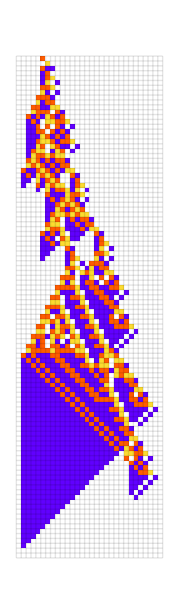

```mathematica
PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-110,110}},<||>],ImageSize->{Automatic,450},Mesh->True]
```

```mathematica
First[][[24]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
First[][[25]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>][[1,26]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,2,1,2,1,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PerturbedCellularAutomaton[{171853175563328300872295216295250029632,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>][[1,26]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,2,1,2,1,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PlotCA[PerturbedCellularAutomaton[{171853175563328300872295216295250029632,4,1},{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]
```

```mathematica
{299459058088077823758143088095350287424,4,1}
```

```mathematica
ResourceFunction["InteractiveListSelector"][PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,300},Mesh->True]->#&/@]
```

```mathematica
IntegerDigits[First@#,4,64]&/@{{299459058088077823758143088095350287424,4,1},{171853175563328300872295216295250029632,4,1},{86782573691888883180616352463682333760,4,1},{86782588903696085919369170424120798272,4,1},{129317879698210992939373390366279003200,4,1}}
```

{{3,2,0,1,1,0,2,1,2,3,1,3,1,3,2,2,0,3,3,1,1,2,2,0,3,2,2,1,0,2,2,0,1,3,1,0,0,1,1,1,2,1,2,3,0,0,1,3,1,1,2,2,1,2,2,0,3,2,3,0,1,0,0,0},{2,0,0,1,1,0,2,1,2,3,1,3,2,3,2,2,0,3,3,1,1,2,2,0,3,2,2,1,0,2,2,0,1,3,1,0,0,1,1,1,2,1,2,3,0,0,1,3,1,1,2,2,1,2,2,0,3,2,3,0,1,0,0,0},{1,0,0,1,1,0,2,1,2,3,1,3,0,3,2,2,0,3,3,1,1,2,2,0,3,2,2,1,0,2,2,0,1,3,1,0,0,1,1,1,2,1,2,3,0,0,1,3,1,1,2,2,1,2,2,0,3,2,3,0,1,0,0,0},{1,0,0,1,1,0,2,1,2,3,1,3,3,3,2,2,0,3,3,1,1,2,2,0,3,2,2,1,0,2,2,0,1,3,1,0,0,1,1,1,2,1,2,3,0,0,1,3,1,1,2,2,1,2,2,0,3,2,3,0,1,0,0,0},{1,2,0,1,1,0,2,1,2,3,1,3,2,3,2,2,0,3,3,1,1,2,2,0,3,2,2,1,0,2,2,0,1,3,1,0,0,1,1,1,2,1,2,3,0,0,1,3,1,1,2,2,1,2,2,0,3,2,3,0,1,0,0,0}}

```mathematica
GraphicsRow[Part[RulePlot[CellularAutomaton[{First@#,4,1}],ColorRules->colorrules][[1,1,All,All,1]]//Flatten,{1,2,13}],Frame->All,ImageSize->120]&/@{{299459058088077823758143088095350287424,4,1},{171853175563328300872295216295250029632,4,1},{86782573691888883180616352463682333760,4,1},{86782588903696085919369170424120798272,4,1},{129317879698210992939373390366279003200,4,1}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
4^3
```

64

```mathematica
PlotCA[PerturbedCellularAutomaton[{86782588903696085919369170424120798272,4,1},{{1},0},{400,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,450},Mesh->True]
```

-Graphics-

```mathematica
PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbedCellularAutomaton[#,{{1},0},{600,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{300,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-200,200}},<|{10,203}->0|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

#### For a single perturbation, what is variation of lifetimes...

```mathematica
TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},<|{23,111}->2|>]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{85,96,60,250,74,66,69,71,-∞,66,74,57,57,57,57,57,85,96,60,388,205,66,69,71,-∞,66,74,57,57,57,57,57,85,96,60,250,75,66,69,71,-∞,66,74,57,57,57,57,57,85,96,60,156,151,66,69,71,-∞,66,74,57,57,57,57,57}

```mathematica
Histogram[%392,{1},PlotRange->{{0,120},Automatic},Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","number of variants"}]
```

-Graphics-

```mathematica
allperts[{299459058088077823758143088095350287424,4,1},{{1},0},{400,{-110,110}}]
```

```mathematica
RandomSample[,10]
```

{<|{68,107}→0|>,<|{59,110}→0|>,<|{32,112}→0|>,<|{90,123}→2|>,<|{53,112}→0|>,<|{69,111}→3|>,<|{37,115}→0|>,<|{61,107}→3|>,<|{87,119}→0|>,<|{69,114}→0|>}

```mathematica
(p|->Histogram[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],{1},Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","number of variants"}])/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<|{61,107}->3|>
```

```mathematica
KeyValueMap[Labeled[#1,Text[StringTemplate["(``)"][#2]]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-110,110}},<|{61,107}->3|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-(64)}

```mathematica
(p|->KeyValueMap[Labeled[#1,Text[StringTemplate["(``)"][#2]]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-110,110}},p],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]])/@
```

{{-Graphics-(64)},{-Graphics-(64)},{-Graphics-(16),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(4),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1)},{-Graphics-(64)},{-Graphics-(16),-Graphics-(16),-Graphics-(16),-Graphics-(16)},{-Graphics-(16),-Graphics-(16),-Graphics-(4),-Graphics-(4),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1)},{-Graphics-(16),-Graphics-(16),-Graphics-(4),-Graphics-(4),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1),-Graphics-(1)},{-Graphics-(64)},{-Graphics-(64)},{-Graphics-(64)}}

```mathematica
Function[p,Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={130,{-110,110}},mca,oca,row,firstbody},mca=PerturbedCellularAutomaton[ru,init,txspec,<|{23,111}->2|>];
oca=PerturbedCellularAutomaton[p,init,txspec,<|{23,111}->2|>];
row=SparseArray[diff=First[mca]-First[oca]]["NonzeroPositions"][[1,1]];
firstbody=nonzeroRange[First[oca][[row]]]//First;
PlotCA[oca,"Graphics"->{Arrowheads[Large],Thick,Red,Arrow[{{30,Length[First[oca]]-row},{18,Length[First[oca]]-row}}]}]]]@quickneutral[{299459058088077823758143088095350287424,4,1}][[1]]
```

-Graphics-

```mathematica
Function[p,Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={130,{-110,110}},mca,oca,row,firstbody},mca=PerturbedCellularAutomaton[ru,init,txspec,<|{23,111}->2|>];
oca=PerturbedCellularAutomaton[p,init,txspec,<|{23,111}->2|>];
row=SparseArray[diff=First[mca]-First[oca]]["NonzeroPositions"][[1,1]];
firstbody=nonzeroRange[First[oca][[row]]]//First;
PlotCA[oca,"Graphics"->{Arrowheads[Large],Thick,Red,Arrow[{{30,Length[First[oca]]-row},{18,Length[First[oca]]-row}}]}]]]@quickneutral[{299459058088077823758143088095350287424,4,1}][[2]]
```

-Graphics-

```mathematica
Function[p,Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={130,{-110,110}},mca,oca,row,firstbody},mca=PerturbedCellularAutomaton[ru,init,txspec,<|{23,111}->2|>];
oca=PerturbedCellularAutomaton[p,init,txspec,<|{23,111}->2|>];
row=SparseArray[diff=First[mca]-First[oca]]["NonzeroPositions"][[1,1]];
firstbody=nonzeroRange[First[oca][[row]]]//First;
PlotCA[oca,"Graphics"->{Arrowheads[Large],Thick,Red,Arrow[{{30,Length[First[oca]]-row},{18,Length[First[oca]]-row}}]}]]]/@quickneutral[{299459058088077823758143088095350287424,4,1}]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Part::partd: Part specification SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«46»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«81»}⟦{}⟦1,1⟧⟧][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«46»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«81»}⟦{}⟦1,1⟧⟧][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Part::partd: Part specification SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«46»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«171»},«81»}⟦{}⟦1,1⟧⟧][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in ….

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Counts[%]
```

<|-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→16,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1|>

```mathematica
Function[p,Histogram[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],{1},PlotRange->{{0,120},Automatic},Frame->True,AspectRatio->.4,PlotTheme->"Minimal"]]/@(SeedRandom[235346];RandomSample[,10])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[,Keys[#][[1,1]]<40&]
```

{<|{0,111}→0|>,<|{0,111}→2|>,<|{0,111}→3|>,<|{1,112}→0|>,<|{1,112}→1|>,<|{1,112}→2|>,<|{2,111}→0|>,<|{2,111}→2|>,<|{2,111}→3|>,<|{2,112}→0|>,<|{2,112}→1|>,<|{2,112}→3|>,<|{2,113}→0|>,<|{2,113}→1|>,<|{2,113}→3|>,<|{3,111}→0|>,<|{3,111}→1|>,<|{3,111}→3|>,<|{3,112}→0|>,<|{3,112}→2|>,<|{3,112}→3|>,<|{4,111}→0|>,<|{4,111}→1|>,<|{4,111}→3|>,<|{4,112}→0|>,<|{4,112}→2|>,<|{4,112}→3|>,<|{4,113}→0|>,<|{4,113}→1|>,<|{4,113}→2|>,<|{5,111}→0|>,<|{5,111}→1|>,<|{5,111}→3|>,<|{5,112}→0|>,<|{5,112}→1|>,<|{5,112}→2|>,<|{5,113}→1|>,<|{5,113}→2|>,<|{5,113}→3|>,<|{5,114}→0|>,<|{5,114}→1|>,<|{5,114}→3|>,<|{6,111}→0|>,<|{6,111}→2|>,<|{6,111}→3|>,<|{6,112}→0|>,<|{6,112}→2|>,<|{6,112}→3|>,<|{6,113}→0|>,<|{6,113}→1|>,<|{6,113}→2|>,<|{7,111}→0|>,<|{7,111}→1|>,<|{7,111}→2|>,<|{7,112}→0|>,<|{7,112}→1|>,<|{7,112}→3|>,<|{7,113}→1|>,<|{7,113}→2|>,<|{7,113}→3|>,<|{7,114}→0|>,<|{7,114}→1|>,<|{7,114}→3|>,<|{8,110}→0|>,<|{8,110}→2|>,<|{8,110}→3|>,<|{8,111}→0|>,<|{8,111}→2|>,<|{8,111}→3|>,<|{8,112}→0|>,<|{8,112}→2|>,<|{8,112}→3|>,<|{8,113}→0|>,<|{8,113}→1|>,<|{8,113}→3|>,<|{9,110}→0|>,<|{9,110}→1|>,<|{9,110}→2|>,<|{9,111}→0|>,<|{9,111}→1|>,<|{9,111}→3|>,<|{9,112}→0|>,<|{9,112}→2|>,<|{9,112}→3|>,<|{9,113}→0|>,<|{9,113}→2|>,<|{9,113}→3|>,<|{10,109}→0|>,<|{10,109}→2|>,<|{10,109}→3|>,<|{10,110}→0|>,<|{10,110}→2|>,<|{10,110}→3|>,<|{10,111}→0|>,<|{10,111}→1|>,<|{10,111}→3|>,<|{10,112}→0|>,<|{10,112}→1|>,<|{10,112}→3|>,<|{10,113}→0|>,<|{10,113}→1|>,<|{10,113}→2|>,<|{10,114}→0|>,<|{10,114}→1|>,<|{10,114}→2|>,<|{11,109}→0|>,<|{11,109}→1|>,<|{11,109}→2|>,<|{11,110}→0|>,<|{11,110}→2|>,<|{11,110}→3|>,<|{11,111}→0|>,<|{11,111}→2|>,<|{11,111}→3|>,<|{11,112}→0|>,<|{11,112}→2|>,<|{11,112}→3|>,<|{11,113}→1|>,<|{11,113}→2|>,<|{11,113}→3|>,<|{11,114}→0|>,<|{11,114}→2|>,<|{11,114}→3|>,<|{11,115}→0|>,<|{11,115}→1|>,<|{11,115}→3|>,<|{12,108}→0|>,<|{12,108}→2|>,<|{12,108}→3|>,<|{12,109}→0|>,<|{12,109}→1|>,<|{12,109}→3|>,<|{12,110}→0|>,<|{12,110}→2|>,<|{12,110}→3|>,<|{12,111}→0|>,<|{12,111}→1|>,<|{12,111}→3|>,<|{12,112}→0|>,<|{12,112}→1|>,<|{12,112}→2|>,<|{12,113}→0|>,<|{12,113}→2|>,<|{12,113}→3|>,<|{12,114}→0|>,<|{12,114}→1|>,<|{12,114}→3|>,<|{12,115}→0|>,<|{12,115}→2|>,<|{12,115}→3|>,<|{13,108}→0|>,<|{13,108}→1|>,<|{13,108}→3|>,<|{13,109}→0|>,<|{13,109}→2|>,<|{13,109}→3|>,<|{13,110}→0|>,<|{13,110}→1|>,<|{13,110}→3|>,<|{13,111}→1|>,<|{13,111}→2|>,<|{13,111}→3|>,<|{13,112}→0|>,<|{13,112}→1|>,<|{13,112}→2|>,<|{13,113}→0|>,<|{13,113}→1|>,<|{13,113}→2|>,<|{13,114}→0|>,<|{13,114}→2|>,<|{13,114}→3|>,<|{13,115}→0|>,<|{13,115}→2|>,<|{13,115}→3|>,<|{13,116}→0|>,<|{13,116}→1|>,<|{13,116}→2|>,<|{14,108}→0|>,<|{14,108}→1|>,<|{14,108}→3|>,<|{14,109}→0|>,<|{14,109}→1|>,<|{14,109}→3|>,<|{14,110}→0|>,<|{14,110}→2|>,<|{14,110}→3|>,<|{14,111}→1|>,<|{14,111}→2|>,<|{14,111}→3|>,<|{14,112}→0|>,<|{14,112}→2|>,<|{14,112}→3|>,<|{14,113}→1|>,<|{14,113}→2|>,<|{14,113}→3|>,<|{14,114}→0|>,<|{14,114}→2|>,<|{14,114}→3|>,<|{14,115}→0|>,<|{14,115}→1|>,<|{14,115}→3|>,<|{14,116}→1|>,<|{14,116}→2|>,<|{14,116}→3|>,<|{14,117}→0|>,<|{14,117}→1|>,<|{14,117}→3|>,<|{15,108}→0|>,<|{15,108}→1|>,<|{15,108}→3|>,<|{15,109}→0|>,<|{15,109}→1|>,<|{15,109}→3|>,<|{15,110}→0|>,<|{15,110}→2|>,<|{15,110}→3|>,<|{15,111}→0|>,<|{15,111}→2|>,<|{15,111}→3|>,<|{15,112}→1|>,<|{15,112}→2|>,<|{15,112}→3|>,<|{15,113}→0|>,<|{15,113}→2|>,<|{15,113}→3|>,<|{15,114}→0|>,<|{15,114}→1|>,<|{15,114}→3|>,<|{15,115}→0|>,<|{15,115}→2|>,<|{15,115}→3|>,<|{15,116}→0|>,<|{15,116}→1|>,<|{15,116}→3|>,<|{16,108}→0|>,<|{16,108}→1|>,<|{16,108}→3|>,<|{16,109}→0|>,<|{16,109}→1|>,<|{16,109}→3|>,<|{16,110}→0|>,<|{16,110}→1|>,<|{16,110}→3|>,<|{16,111}→0|>,<|{16,111}→1|>,<|{16,111}→2|>,<|{16,112}→0|>,<|{16,112}→2|>,<|{16,112}→3|>,<|{16,113}→0|>,<|{16,113}→1|>,<|{16,113}→3|>,<|{16,114}→0|>,<|{16,114}→2|>,<|{16,114}→3|>,<|{16,115}→0|>,<|{16,115}→1|>,<|{16,115}→3|>,<|{16,116}→0|>,<|{16,116}→2|>,<|{16,116}→3|>,<|{17,108}→0|>,<|{17,108}→1|>,<|{17,108}→3|>,<|{17,109}→0|>,<|{17,109}→1|>,<|{17,109}→3|>,<|{17,110}→0|>,<|{17,110}→2|>,<|{17,110}→3|>,<|{17,111}→0|>,<|{17,111}→1|>,<|{17,111}→2|>,<|{17,112}→0|>,<|{17,112}→1|>,<|{17,112}→2|>,<|{17,113}→0|>,<|{17,113}→2|>,<|{17,113}→3|>,<|{17,114}→0|>,<|{17,114}→1|>,<|{17,114}→3|>,<|{17,115}→0|>,<|{17,115}→2|>,<|{17,115}→3|>,<|{17,116}→0|>,<|{17,116}→2|>,<|{17,116}→3|>,<|{17,117}→0|>,<|{17,117}→1|>,<|{17,117}→2|>,<|{18,108}→0|>,<|{18,108}→1|>,<|{18,108}→3|>,<|{18,109}→0|>,<|{18,109}→1|>,<|{18,109}→3|>,<|{18,110}→0|>,<|{18,110}→1|>,<|{18,110}→2|>,<|{18,111}→0|>,<|{18,111}→2|>,<|{18,111}→3|>,<|{18,112}→1|>,<|{18,112}→2|>,<|{18,112}→3|>,<|{18,113}→0|>,<|{18,113}→1|>,<|{18,113}→2|>,<|{18,114}→0|>,<|{18,114}→2|>,<|{18,114}→3|>,<|{18,115}→0|>,<|{18,115}→1|>,<|{18,115}→3|>,<|{18,116}→0|>,<|{18,116}→1|>,<|{18,116}→3|>,<|{18,117}→1|>,<|{18,117}→2|>,<|{18,117}→3|>,<|{18,118}→0|>,<|{18,118}→1|>,<|{18,118}→3|>,<|{19,108}→0|>,<|{19,108}→1|>,<|{19,108}→3|>,<|{19,109}→0|>,<|{19,109}→2|>,<|{19,109}→3|>,<|{19,110}→0|>,<|{19,110}→1|>,<|{19,110}→2|>,<|{19,111}→0|>,<|{19,111}→1|>,<|{19,111}→2|>,<|{19,112}→1|>,<|{19,112}→2|>,<|{19,112}→3|>,<|{19,113}→0|>,<|{19,113}→1|>,<|{19,113}→3|>,<|{19,114}→0|>,<|{19,114}→1|>,<|{19,114}→2|>,<|{19,115}→0|>,<|{19,115}→2|>,<|{19,115}→3|>,<|{19,116}→1|>,<|{19,116}→2|>,<|{19,116}→3|>,<|{19,117}→0|>,<|{19,117}→1|>,<|{19,117}→3|>,<|{20,108}→0|>,<|{20,108}→1|>,<|{20,108}→3|>,<|{20,109}→0|>,<|{20,109}→1|>,<|{20,109}→2|>,<|{20,110}→0|>,<|{20,110}→2|>,<|{20,110}→3|>,<|{20,111}→0|>,<|{20,111}→2|>,<|{20,111}→3|>,<|{20,112}→0|>,<|{20,112}→1|>,<|{20,112}→2|>,<|{20,113}→0|>,<|{20,113}→2|>,<|{20,113}→3|>,<|{20,114}→0|>,<|{20,114}→1|>,<|{20,114}→2|>,<|{20,115}→0|>,<|{20,115}→1|>,<|{20,115}→2|>,<|{21,108}→0|>,<|{21,108}→2|>,<|{21,108}→3|>,<|{21,109}→0|>,<|{21,109}→1|>,<|{21,109}→2|>,<|{21,110}→0|>,<|{21,110}→2|>,<|{21,110}→3|>,<|{21,111}→0|>,<|{21,111}→1|>,<|{21,111}→3|>,<|{21,112}→0|>,<|{21,112}→2|>,<|{21,112}→3|>,<|{21,113}→0|>,<|{21,113}→1|>,<|{21,113}→3|>,<|{21,114}→0|>,<|{21,114}→2|>,<|{21,114}→3|>,<|{21,115}→0|>,<|{21,115}→2|>,<|{21,115}→3|>,<|{21,116}→0|>,<|{21,116}→1|>,<|{21,116}→3|>,<|{22,108}→0|>,<|{22,108}→1|>,<|{22,108}→2|>,<|{22,109}→0|>,<|{22,109}→2|>,<|{22,109}→3|>,<|{22,110}→0|>,<|{22,110}→1|>,<|{22,110}→2|>,<|{22,111}→0|>,<|{22,111}→2|>,<|{22,111}→3|>,<|{22,112}→0|>,<|{22,112}→1|>,<|{22,112}→3|>,<|{22,113}→0|>,<|{22,113}→2|>,<|{22,113}→3|>,<|{22,114}→0|>,<|{22,114}→1|>,<|{22,114}→3|>,<|{22,115}→0|>,<|{22,115}→2|>,<|{22,115}→3|>,<|{22,116}→0|>,<|{22,116}→2|>,<|{22,116}→3|>,<|{23,107}→0|>,<|{23,107}→2|>,<|{23,107}→3|>,<|{23,108}→0|>,<|{23,108}→1|>,<|{23,108}→3|>,<|{23,109}→0|>,<|{23,109}→1|>,<|{23,109}→3|>,<|{23,110}→0|>,<|{23,110}→2|>,<|{23,110}→3|>,<|{23,111}→0|>,<|{23,111}→1|>,<|{23,111}→2|>,<|{23,112}→0|>,<|{23,112}→2|>,<|{23,112}→3|>,<|{23,113}→0|>,<|{23,113}→1|>,<|{23,113}→3|>,<|{23,114}→0|>,<|{23,114}→2|>,<|{23,114}→3|>,<|{23,115}→0|>,<|{23,115}→1|>,<|{23,115}→3|>,<|{23,116}→0|>,<|{23,116}→1|>,<|{23,116}→2|>,<|{23,117}→0|>,<|{23,117}→1|>,<|{23,117}→2|>,<|{24,107}→0|>,<|{24,107}→1|>,<|{24,107}→3|>,<|{24,108}→0|>,<|{24,108}→2|>,<|{24,108}→3|>,<|{24,109}→0|>,<|{24,109}→1|>,<|{24,109}→3|>,<|{24,110}→0|>,<|{24,110}→1|>,<|{24,110}→2|>,<|{24,111}→0|>,<|{24,111}→2|>,<|{24,111}→3|>,<|{24,112}→0|>,<|{24,112}→1|>,<|{24,112}→2|>,<|{24,113}→0|>,<|{24,113}→2|>,<|{24,113}→3|>,<|{24,114}→0|>,<|{24,114}→1|>,<|{24,114}→3|>,<|{24,115}→1|>,<|{24,115}→2|>,<|{24,115}→3|>,<|{24,116}→1|>,<|{24,116}→2|>,<|{24,116}→3|>,<|{24,117}→0|>,<|{24,117}→2|>,<|{24,117}→3|>,<|{24,118}→0|>,<|{24,118}→1|>,<|{24,118}→3|>,<|{25,107}→0|>,<|{25,107}→1|>,<|{25,107}→3|>,<|{25,108}→0|>,<|{25,108}→1|>,<|{25,108}→3|>,<|{25,109}→1|>,<|{25,109}→2|>,<|{25,109}→3|>,<|{25,110}→0|>,<|{25,110}→1|>,<|{25,110}→2|>,<|{25,111}→0|>,<|{25,111}→1|>,<|{25,111}→3|>,<|{25,112}→0|>,<|{25,112}→2|>,<|{25,112}→3|>,<|{25,113}→0|>,<|{25,113}→1|>,<|{25,113}→2|>,<|{25,114}→0|>,<|{25,114}→2|>,<|{25,114}→3|>,<|{25,115}→1|>,<|{25,115}→2|>,<|{25,115}→3|>,<|{25,116}→1|>,<|{25,116}→2|>,<|{25,116}→3|>,<|{25,117}→0|>,<|{25,117}→1|>,<|{25,117}→3|>,<|{25,118}→0|>,<|{25,118}→2|>,<|{25,118}→3|>,<|{26,107}→0|>,<|{26,107}→1|>,<|{26,107}→3|>,<|{26,108}→1|>,<|{26,108}→2|>,<|{26,108}→3|>,<|{26,109}→1|>,<|{26,109}→2|>,<|{26,109}→3|>,<|{26,110}→0|>,<|{26,110}→2|>,<|{26,110}→3|>,<|{26,111}→0|>,<|{26,111}→1|>,<|{26,111}→3|>,<|{26,112}→0|>,<|{26,112}→1|>,<|{26,112}→2|>,<|{26,113}→0|>,<|{26,113}→2|>,<|{26,113}→3|>,<|{26,114}→0|>,<|{26,114}→1|>,<|{26,114}→2|>,<|{26,115}→0|>,<|{26,115}→1|>,<|{26,115}→2|>,<|{26,116}→1|>,<|{26,116}→2|>,<|{26,116}→3|>,<|{26,117}→0|>,<|{26,117}→1|>,<|{26,117}→3|>,<|{26,118}→0|>,<|{26,118}→2|>,<|{26,118}→3|>,<|{26,119}→0|>,<|{26,119}→1|>,<|{26,119}→2|>,<|{27,110}→0|>,<|{27,110}→1|>,<|{27,110}→3|>,<|{27,111}→1|>,<|{27,111}→2|>,<|{27,111}→3|>,<|{27,112}→0|>,<|{27,112}→1|>,<|{27,112}→2|>,<|{27,113}→0|>,<|{27,113}→1|>,<|{27,113}→3|>,<|{27,114}→0|>,<|{27,114}→2|>,<|{27,114}→3|>,<|{27,115}→0|>,<|{27,115}→2|>,<|{27,115}→3|>,<|{27,116}→0|>,<|{27,116}→1|>,<|{27,116}→2|>,<|{27,117}→0|>,<|{27,117}→1|>,<|{27,117}→3|>,<|{27,118}→0|>,<|{27,118}→1|>,<|{27,118}→2|>,<|{27,119}→1|>,<|{27,119}→2|>,<|{27,119}→3|>,<|{27,120}→0|>,<|{27,120}→1|>,<|{27,120}→3|>,<|{28,112}→0|>,<|{28,112}→2|>,<|{28,112}→3|>,<|{28,113}→0|>,<|{28,113}→1|>,<|{28,113}→3|>,<|{28,114}→0|>,<|{28,114}→1|>,<|{28,114}→3|>,<|{28,115}→0|>,<|{28,115}→1|>,<|{28,115}→3|>,<|{28,116}→0|>,<|{28,116}→1|>,<|{28,116}→2|>,<|{28,117}→0|>,<|{28,117}→2|>,<|{28,117}→3|>,<|{28,118}→0|>,<|{28,118}→2|>,<|{28,118}→3|>,<|{28,119}→0|>,<|{28,119}→1|>,<|{28,119}→2|>,<|{29,112}→0|>,<|{29,112}→1|>,<|{29,112}→3|>,<|{29,113}→0|>,<|{29,113}→2|>,<|{29,113}→3|>,<|{29,114}→0|>,<|{29,114}→1|>,<|{29,114}→3|>,<|{29,115}→0|>,<|{29,115}→2|>,<|{29,115}→3|>,<|{29,116}→0|>,<|{29,116}→1|>,<|{29,116}→2|>,<|{29,117}→0|>,<|{29,117}→2|>,<|{29,117}→3|>,<|{29,118}→0|>,<|{29,118}→1|>,<|{29,118}→3|>,<|{29,119}→1|>,<|{29,119}→2|>,<|{29,119}→3|>,<|{29,120}→0|>,<|{29,120}→1|>,<|{29,120}→3|>,<|{30,112}→0|>,<|{30,112}→1|>,<|{30,112}→3|>,<|{30,113}→0|>,<|{30,113}→1|>,<|{30,113}→3|>,<|{30,114}→0|>,<|{30,114}→2|>,<|{30,114}→3|>,<|{30,115}→0|>,<|{30,115}→1|>,<|{30,115}→2|>,<|{30,116}→0|>,<|{30,116}→2|>,<|{30,116}→3|>,<|{30,117}→0|>,<|{30,117}→1|>,<|{30,117}→2|>,<|{30,118}→0|>,<|{30,118}→2|>,<|{30,118}→3|>,<|{30,119}→0|>,<|{30,119}→1|>,<|{30,119}→3|>,<|{31,112}→0|>,<|{31,112}→1|>,<|{31,112}→3|>,<|{31,113}→0|>,<|{31,113}→1|>,<|{31,113}→3|>,<|{31,114}→0|>,<|{31,114}→1|>,<|{31,114}→2|>,<|{31,115}→0|>,<|{31,115}→2|>,<|{31,115}→3|>,<|{31,116}→0|>,<|{31,116}→1|>,<|{31,116}→3|>,<|{31,117}→0|>,<|{31,117}→2|>,<|{31,117}→3|>,<|{31,118}→0|>,<|{31,118}→1|>,<|{31,118}→2|>,<|{31,119}→0|>,<|{31,119}→2|>,<|{31,119}→3|>,<|{32,112}→0|>,<|{32,112}→1|>,<|{32,112}→3|>,<|{32,113}→0|>,<|{32,113}→2|>,<|{32,113}→3|>,<|{32,114}→0|>,<|{32,114}→1|>,<|{32,114}→2|>,<|{32,115}→0|>,<|{32,115}→1|>,<|{32,115}→2|>,<|{32,116}→0|>,<|{32,116}→2|>,<|{32,116}→3|>,<|{32,117}→0|>,<|{32,117}→1|>,<|{32,117}→2|>,<|{32,118}→0|>,<|{32,118}→2|>,<|{32,118}→3|>,<|{32,119}→0|>,<|{32,119}→1|>,<|{32,119}→2|>,<|{32,120}→0|>,<|{32,120}→1|>,<|{32,120}→2|>,<|{33,112}→0|>,<|{33,112}→1|>,<|{33,112}→3|>,<|{33,113}→0|>,<|{33,113}→1|>,<|{33,113}→2|>,<|{33,114}→0|>,<|{33,114}→2|>,<|{33,114}→3|>,<|{33,115}→1|>,<|{33,115}→2|>,<|{33,115}→3|>,<|{33,116}→0|>,<|{33,116}→1|>,<|{33,116}→3|>,<|{33,117}→0|>,<|{33,117}→2|>,<|{33,117}→3|>,<|{33,118}→0|>,<|{33,118}→1|>,<|{33,118}→3|>,<|{33,119}→0|>,<|{33,119}→2|>,<|{33,119}→3|>,<|{33,120}→0|>,<|{33,120}→2|>,<|{33,120}→3|>,<|{33,121}→0|>,<|{33,121}→1|>,<|{33,121}→3|>,<|{34,112}→0|>,<|{34,112}→2|>,<|{34,112}→3|>,<|{34,113}→0|>,<|{34,113}→1|>,<|{34,113}→2|>,<|{34,114}→0|>,<|{34,114}→1|>,<|{34,114}→2|>,<|{34,115}→1|>,<|{34,115}→2|>,<|{34,115}→3|>,<|{34,116}→0|>,<|{34,116}→1|>,<|{34,116}→3|>,<|{34,117}→0|>,<|{34,117}→1|>,<|{34,117}→3|>,<|{34,118}→0|>,<|{34,118}→2|>,<|{34,118}→3|>,<|{34,119}→0|>,<|{34,119}→1|>,<|{34,119}→3|>,<|{34,120}→0|>,<|{34,120}→2|>,<|{34,120}→3|>,<|{34,121}→0|>,<|{34,121}→2|>,<|{34,121}→3|>,<|{35,112}→0|>,<|{35,112}→1|>,<|{35,112}→2|>,<|{35,113}→0|>,<|{35,113}→2|>,<|{35,113}→3|>,<|{35,114}→0|>,<|{35,114}→2|>,<|{35,114}→3|>,<|{35,115}→0|>,<|{35,115}→1|>,<|{35,115}→2|>,<|{35,116}→0|>,<|{35,116}→1|>,<|{35,116}→3|>,<|{35,117}→0|>,<|{35,117}→1|>,<|{35,117}→3|>,<|{35,118}→0|>,<|{35,118}→1|>,<|{35,118}→3|>,<|{35,119}→0|>,<|{35,119}→2|>,<|{35,119}→3|>,<|{35,120}→0|>,<|{35,120}→1|>,<|{35,120}→3|>,<|{35,121}→0|>,<|{35,121}→1|>,<|{35,121}→2|>,<|{35,122}→0|>,<|{35,122}→1|>,<|{35,122}→2|>,<|{36,111}→0|>,<|{36,111}→2|>,<|{36,111}→3|>,<|{36,112}→0|>,<|{36,112}→1|>,<|{36,112}→3|>,<|{36,113}→0|>,<|{36,113}→2|>,<|{36,113}→3|>,<|{36,114}→0|>,<|{36,114}→1|>,<|{36,114}→3|>,<|{36,115}→0|>,<|{36,115}→1|>,<|{36,115}→2|>,<|{36,116}→1|>,<|{36,116}→2|>,<|{36,116}→3|>,<|{36,117}→0|>,<|{36,117}→1|>,<|{36,117}→3|>,<|{36,118}→0|>,<|{36,118}→1|>,<|{36,118}→3|>,<|{36,119}→0|>,<|{36,119}→1|>,<|{36,119}→3|>,<|{36,120}→1|>,<|{36,120}→2|>,<|{36,120}→3|>,<|{36,121}→1|>,<|{36,121}→2|>,<|{36,121}→3|>,<|{36,122}→0|>,<|{36,122}→2|>,<|{36,122}→3|>,<|{36,123}→0|>,<|{36,123}→1|>,<|{36,123}→3|>,<|{37,111}→0|>,<|{37,111}→1|>,<|{37,111}→3|>,<|{37,112}→0|>,<|{37,112}→2|>,<|{37,112}→3|>,<|{37,113}→0|>,<|{37,113}→1|>,<|{37,113}→3|>,<|{37,114}→1|>,<|{37,114}→2|>,<|{37,114}→3|>,<|{37,115}→0|>,<|{37,115}→2|>,<|{37,115}→3|>,<|{37,116}→0|>,<|{37,116}→1|>,<|{37,116}→2|>,<|{37,117}→0|>,<|{37,117}→1|>,<|{37,117}→3|>,<|{37,118}→0|>,<|{37,118}→1|>,<|{37,118}→3|>,<|{37,119}→1|>,<|{37,119}→2|>,<|{37,119}→3|>,<|{37,120}→1|>,<|{37,120}→2|>,<|{37,120}→3|>,<|{37,121}→1|>,<|{37,121}→2|>,<|{37,121}→3|>,<|{37,122}→0|>,<|{37,122}→1|>,<|{37,122}→3|>,<|{37,123}→0|>,<|{37,123}→2|>,<|{37,123}→3|>,<|{38,111}→0|>,<|{38,111}→1|>,<|{38,111}→3|>,<|{38,112}→0|>,<|{38,112}→1|>,<|{38,112}→3|>,<|{38,113}→0|>,<|{38,113}→2|>,<|{38,113}→3|>,<|{38,114}→0|>,<|{38,114}→1|>,<|{38,114}→3|>,<|{38,115}→0|>,<|{38,115}→1|>,<|{38,115}→2|>,<|{38,116}→0|>,<|{38,116}→1|>,<|{38,116}→2|>,<|{38,117}→1|>,<|{38,117}→2|>,<|{38,117}→3|>,<|{38,118}→1|>,<|{38,118}→2|>,<|{38,118}→3|>,<|{38,119}→1|>,<|{38,119}→2|>,<|{38,119}→3|>,<|{38,120}→1|>,<|{38,120}→2|>,<|{38,120}→3|>,<|{38,121}→1|>,<|{38,121}→2|>,<|{38,121}→3|>,<|{38,122}→0|>,<|{38,122}→1|>,<|{38,122}→3|>,<|{38,123}→0|>,<|{38,123}→2|>,<|{38,123}→3|>,<|{38,124}→0|>,<|{38,124}→1|>,<|{38,124}→2|>,<|{39,111}→0|>,<|{39,111}→1|>,<|{39,111}→3|>,<|{39,112}→0|>,<|{39,112}→1|>,<|{39,112}→3|>,<|{39,113}→0|>,<|{39,113}→1|>,<|{39,113}→3|>,<|{39,114}→1|>,<|{39,114}→2|>,<|{39,114}→3|>,<|{39,115}→1|>,<|{39,115}→2|>,<|{39,115}→3|>,<|{39,116}→0|>,<|{39,116}→2|>,<|{39,116}→3|>,<|{39,117}→0|>,<|{39,117}→1|>,<|{39,117}→3|>,<|{39,118}→1|>,<|{39,118}→2|>,<|{39,118}→3|>,<|{39,119}→1|>,<|{39,119}→2|>,<|{39,119}→3|>,<|{39,120}→1|>,<|{39,120}→2|>,<|{39,120}→3|>,<|{39,121}→1|>,<|{39,121}→2|>,<|{39,121}→3|>,<|{39,122}→0|>,<|{39,122}→1|>,<|{39,122}→3|>,<|{39,123}→0|>,<|{39,123}→1|>,<|{39,123}→2|>,<|{39,124}→1|>,<|{39,124}→2|>,<|{39,124}→3|>,<|{39,125}→0|>,<|{39,125}→1|>,<|{39,125}→3|>}

```mathematica
Function[p,Histogram[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],{1},PlotRange->{{0,120},Automatic},Frame->True,AspectRatio->.4,PlotTheme->"Minimal"]]/@(SeedRandom[235346];RandomSample[,10])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[p,DeleteCases[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],-Infinity]]/@(SeedRandom[235346];RandomSample[,10])
```

{{102,134,135,99,246,167,135,99,226,207,135,99,242,157,135,99,106,108,135,179,314,231,135,215,111,135,135,251,113,123,135,266,103,124,135,261,131,183,135,227,226,197,135,121,247,200,135,230,380,80,135,140,366,107,135,329,105,100,135,130,166,76,135,297},{33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33},{100,168,230,214,182,161,211,183,149,137,140,214,146,148,181,162,175,103,242,317,100,253,112,186,178,117,111,113,135,153,112,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,80,143,214,112,73,302,68,221,185,113,119,136,77,252,101},{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50},{169,169,169,169,169,169,169,169,169,169,169,169,169,169,169,169,157,141,112,105,284,170,112,105,69,78,286,105,107,117,41,43,131,103,41,43,131,74,41,43,93,73,41,43,208,90,124,66,66,78,144,82,103,247,87,207,115,86,174,168,150,151},{174,176,174,180,174,207,196,285,174,291,174,174,186,254,110,140,174,174,140,167,317,140,207,174,174,140,124,242,174,134,174,159,174,134,196,283,174,134,169,174,174,134,254,212,182,174,207,174,222,170,174,148,200,174,174,219,189,246},{36,133,36,70,36,172,36,97,36,109,36,138,36,74,36,304,36,91,36,70,36,172,36,97,36,109,36,138,36,74,36,219,36,166,36,70,36,172,36,97,36,253,36,138,36,74,36,304,36,118,36,70,36,172,36,97,36,141,36,138,36,74,36,335},{183,128,76,92,366,157,174,92,56,65,140,86,158,144,128,99,92,271,157,99,92,56,65,273,92,94,104,183,128,76,92,230,157,174,92,56,65,86,86,158,196,128,99,92,157,244,92,56,65,258,92,144,148},{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40},{60,60,60,60,53,53,53,53,316,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60}}

```mathematica
DistributionChart[%,ChartElementFunction->"HistogramDensity"]
```

-Graphics-

```mathematica
Function[p,DeleteCases[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],-Infinity]]/@(SeedRandom[235346];RandomSample[,30])
```

{{102,134,135,99,246,167,135,99,226,207,135,99,242,157,135,99,106,108,135,179,314,231,135,215,111,135,135,251,113,123,135,266,103,124,135,261,131,183,135,227,226,197,135,121,247,200,135,230,380,80,135,140,366,107,135,329,105,100,135,130,166,76,135,297},{33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33},{100,168,230,214,182,161,211,183,149,137,140,214,146,148,181,162,175,103,242,317,100,253,112,186,178,117,111,113,135,153,112,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,80,143,214,112,73,302,68,221,185,113,119,136,77,252,101},{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50},{169,169,169,169,169,169,169,169,169,169,169,169,169,169,169,169,157,141,112,105,284,170,112,105,69,78,286,105,107,117,41,43,131,103,41,43,131,74,41,43,93,73,41,43,208,90,124,66,66,78,144,82,103,247,87,207,115,86,174,168,150,151},{174,176,174,180,174,207,196,285,174,291,174,174,186,254,110,140,174,174,140,167,317,140,207,174,174,140,124,242,174,134,174,159,174,134,196,283,174,134,169,174,174,134,254,212,182,174,207,174,222,170,174,148,200,174,174,219,189,246},{36,133,36,70,36,172,36,97,36,109,36,138,36,74,36,304,36,91,36,70,36,172,36,97,36,109,36,138,36,74,36,219,36,166,36,70,36,172,36,97,36,253,36,138,36,74,36,304,36,118,36,70,36,172,36,97,36,141,36,138,36,74,36,335},{183,128,76,92,366,157,174,92,56,65,140,86,158,144,128,99,92,271,157,99,92,56,65,273,92,94,104,183,128,76,92,230,157,174,92,56,65,86,86,158,196,128,99,92,157,244,92,56,65,258,92,144,148},{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40},{60,60,60,60,53,53,53,53,316,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60,60,60,60,60,53,53,53,53,83,94,94,60,60,60,60},{44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,214,196,43,88,214,216,43,179,214,221,43,81,214,137,43,90,220,36,153,72,118,36,61,72,150,36,72,150,36,80,72},{118,91,77,96,175,88,95,169,85,96,96,161,122,144,293,118,91,77,96,93,88,95,169,309,85,96,96,194,113,128,208,118,91,77,96,175,88,95,169,85,96,96,161,122,144,293,118,91,77,96,92,88,95,169,85,96,96,177,127,324},{287,114,117,160,384,135,197,183,134,144,97,157,188,135,135,149,177,114,117,160,291,135,188,183,134,172,184,188,135,135,149,101,114,117,160,341,135,197,183,134,93,230,188,135,135,149,281,114,117,160,135,221,183,134,149,147,157,188,135,135,149},{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40},{83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83},{71,54,50,171,71,54,50,199,71,54,50,168,71,54,50,280,71,54,50,108,71,54,50,108,71,54,50,108,71,54,50,108,71,54,50,129,71,54,50,220,71,54,50,122,71,54,50,131,71,54,50,150,71,54,50,150,71,54,50,150,71,54,50,150},{30,105,49,34,170,170,170,170,33,33,33,33,142,121,122,197,30,49,62,170,170,170,170,33,33,33,33,142,121,122,128,30,106,49,223,170,170,170,170,33,33,33,33,142,121,122,197,30,127,49,57,170,170,170,170,33,33,33,33,142,121,122,239},{153,136,54,61,87,136,54,61,54,136,54,61,82,136,54,61,153,212,54,61,87,215,54,61,54,147,54,61,82,153,54,61,153,117,54,61,87,118,54,61,54,121,54,61,82,148,54,61,153,117,54,61,87,117,54,61,54,117,54,61,82,117,54,61},{50,50,50,50,366,71,81,82,54,54,54,54,59,59,59,59,107,205,76,157,119,174,119,258,71,80,355,118,160,206,164,69,82,150,251,76,230,156,298,80,146,299,80,199,57,62,260,62,57,62,150,62,57,62,62,57,62,62},{42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,355,147,146,173,142,127,279,173,128,84,186,284,162,230,46,43,172,256,46,43,172,122,46,43,172,119,46,43,172,350,133,79,52,72,133,153,52,72,133,99,52,72,133,153,52,72},{44,172,44,272,167,202,167,186,40,87,40,68,39,39,71,44,118,44,272,181,219,181,198,40,127,40,68,39,104,39,71,44,172,44,272,167,202,167,161,40,87,40,68,39,175,39,71,44,64,44,272,198,66,185,390,40,70,40,68,39,78,39,71},{50,37,42,137,50,37,42,311,50,37,42,165,50,37,42,137,50,37,42,137,50,37,42,179,50,37,42,161,50,37,42,137,50,37,42,137,50,37,42,213,50,37,42,115,50,37,42,137,50,37,42,137,50,37,42,216,50,37,42,90,50,37,42,137},{47,47,47,47,47,47,47,47,129,129,129,129,80,70,178,141,91,80,101,164,126,233,187,40,40,40,40,248,131,71,151,60,60,60,60,47,47,47,47,60,60,60,60,139,60,42,281,119,119,119,119,330,80,192,74,138,106,59,77,197,33,38,124},{101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101},{313,50,47,167,156,48,45,40,46,46,46,46,93,49,44,211,171,50,47,167,150,48,45,40,46,46,46,46,68,49,44,157,50,47,167,156,48,45,40,46,46,46,46,93,49,44,211,50,47,167,95,48,45,40,46,46,46,46,71,49,44,201},{73,52,48,96,128,52,48,149,119,52,48,51,242,52,48,60,52,48,152,166,52,48,149,89,52,48,51,310,52,48,60,50,52,48,58,70,52,48,149,255,52,48,51,54,52,48,60,275,52,48,81,138,52,48,149,52,48,51,41,52,48,60},{40,229,57,57,40,197,57,77,40,155,57,78,40,197,57,94,217,103,147,72,207,184,312,72,229,72,62,138,91,72,40,231,57,57,40,197,57,77,40,276,57,78,40,197,57,94,57,60,58,215,50,142,142,169,247,199,198,125,139,219,342,93},{117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117,117},{101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101},{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50}}

```mathematica
DistributionChart[%428,ChartElementFunction->"HistogramDensity",AspectRatio->.3]
```

-Graphics-

```mathematica
apx=allperts[{299459058088077823758143088095350287424,4,1},{{1},0},{200,{-110,110}}];
```

```mathematica
DistributionChart[Function[p,DeleteCases[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],-Infinity]]/@(SeedRandom[235346];RandomSample[apx,30]),ChartElementFunction->"HistogramDensity",AspectRatio->.3]
```

-Graphics-

```mathematica
DistributionChart[Function[p,DeleteCases[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],-Infinity]]/@(SeedRandom[235346];SortBy[RandomSample[apx,30],Keys]),ChartElementFunction->"HistogramDensity",AspectRatio->.3]
```

-Graphics-

```mathematica
DistributionChart[Function[p,DeleteCases[TestCALifeTime[First@PerturbedCellularAutomaton[#,{{1},0},{400,{-110,110}},p]]&/@quickneutral[{299459058088077823758143088095350287424,4,1}],-Infinity]]/@(SeedRandom[237346];SortBy[RandomSample[Select[apx,Keys[#][[1,1]]<40&],30],Keys]),ChartElementFunction->"HistogramDensity",AspectRatio->.3]
```

-Graphics-

```mathematica
quickneutral[{299459058088077823758143088095350287424,4,1}]
```

{{1711981961654267314772700605740280896,4,1},{1711987032256668227690306592553102400,4,1},{1711992102859069140607912579365923904,4,1},{1711997173461470053525518566178745408,4,1},{22979629894212921281233613570225794112,4,1},{22979634964815322194151219557038615616,4,1},{22979640035417723107068825543851437120,4,1},{22979645106020124019986431530664258624,4,1},{44247277826771575247694526534711307328,4,1},{44247282897373976160612132521524128832,4,1},{44247287967976377073529738508336950336,4,1},{44247293038578777986447344495149771840,4,1},{65514925759330229214155439499196820544,4,1},{65514930829932630127073045486009642048,4,1},{65514935900535031039990651472822463552,4,1},{65514940971137431952908257459635285056,4,1},{86782573691888883180616352463682333760,4,1},{86782578762491284093533958450495155264,4,1},{86782583833093685006451564437307976768,4,1},{86782588903696085919369170424120798272,4,1},{108050221624447537147077265428167846976,4,1},{108050226695049938059994871414980668480,4,1},{108050231765652338972912477401793489984,4,1},{108050236836254739885830083388606311488,4,1},{129317869557006191113538178392653360192,4,1},{129317874627608592026455784379466181696,4,1},{129317879698210992939373390366279003200,4,1},{129317884768813393852290996353091824704,4,1},{150585517489564845079999091357138873408,4,1},{150585522560167245992916697343951694912,4,1},{150585527630769646905834303330764516416,4,1},{150585532701372047818751909317577337920,4,1},{171853165422123499046460004321624386624,4,1},{171853170492725899959377610308437208128,4,1},{171853175563328300872295216295250029632,4,1},{171853180633930701785212822282062851136,4,1},{193120813354682153012920917286109899840,4,1},{193120818425284553925838523272922721344,4,1},{193120823495886954838756129259735542848,4,1},{193120828566489355751673735246548364352,4,1},{214388461287240806979381830250595413056,4,1},{214388466357843207892299436237408234560,4,1},{214388471428445608805217042224221056064,4,1},{214388476499048009718134648211033877568,4,1},{235656109219799460945842743215080926272,4,1},{235656114290401861858760349201893747776,4,1},{235656119361004262771677955188706569280,4,1},{235656124431606663684595561175519390784,4,1},{256923757152358114912303656179566439488,4,1},{256923762222960515825221262166379260992,4,1},{256923767293562916738138868153192082496,4,1},{256923772364165317651056474140004904000,4,1},{278191405084916768878764569144051952704,4,1},{278191410155519169791682175130864774208,4,1},{278191415226121570704599781117677595712,4,1},{278191420296723971617517387104490417216,4,1},{299459053017475422845225482108537465920,4,1},{299459058088077823758143088095350287424,4,1},{299459063158680224671060694082163108928,4,1},{299459068229282625583978300068975930432,4,1},{320726700950034076811686395073022979136,4,1},{320726706020636477724604001059835800640,4,1},{320726711091238878637521607046648622144,4,1},{320726716161841279550439213033461443648,4,1}}

```mathematica
Position[quickneutral[{299459058088077823758143088095350287424,4,1}],{299459058088077823758143088095350287424,4,1}]
```

{{58}}

```mathematica
poplts=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={400,{-110,110}},ca,aps},
ParallelMap[Function[rule,ca=CellularAutomaton[rule,init,txspec];
aps=allperts[ca,4];
TestCALifeTime[PerturbedCellularAutomaton[rule,init,txspec,#]]&/@aps],quickneutral[ru]]];
```

```mathematica
Histogram/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[poplts]
```

-Graphics-

```mathematica
Histogram[poplts,{1}]
```

-Graphics-

```mathematica
Histogram[poplts,{1},ChartLayout->"Stacked"]
```

-Graphics-

```mathematica
Union[poplts]//Length
```

64

```mathematica
GraphicsGrid[Partition[Histogram[#,{4},"CDF",PlotTheme->"Minimal",Axes->None,PlotRange->{{0,200},Automatic}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Histogram[#,{4},"SF",PlotTheme->"Minimal",Axes->None,PlotRange->{{0,200},Automatic}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Histogram[#,{4},{"Log","Probability"},PlotTheme->"Minimal",PlotRange->{{0,200},Automatic}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
orig=poplts[[58]];
```

```mathematica
origcdf=Accumulate[BinCounts[orig,{1,200,1}]]
```

{2,3,4,6,8,9,10,12,14,15,15,17,18,18,21,25,26,30,30,33,35,37,43,48,51,56,60,69,72,78,82,89,98,103,111,116,120,129,138,146,146,157,162,174,181,202,210,220,232,239,247,250,253,262,274,282,308,319,334,342,353,361,372,380,392,406,435,455,458,470,479,489,496,505,509,517,526,533,542,558,566,578,595,601,624,637,656,663,694,709,723,743,766,782,801,810,836,851,892,1314,1736,1851,1901,1942,1998,2223,2460,2503,2522,2568,2677,2724,2760,2801,2902,2918,2977,3004,3028,3072,3097,3181,3212,3230,3306,3329,3349,3365,3379,3396,3421,3444,3458,3480,3512,3530,3540,3572,3601,3652,3666,3678,3679,3694,3708,3726,3736,3747,3759,3766,3771,3777,3785,3790,3798,3808,3830,3851,3856,3861,3871,3882,3884,3901,3902,3909,3924,3928,3934,3938,3944,3955,3968,3975,3983,3987,3990,4001,4008,4031,4034,4039,4049,4055,4069,4074,4085,4099,4125,4142,4158,4166,4186,4201,4205,4210,4216,4219,4222}

```mathematica
Total[poplts[[58]]]
```

498961

```mathematica
origsf=(Last[#]-#)&[Accumulate[BinCounts[poplts[[58]],{1,200,1}]]];
```

```mathematica
ListStepPlot[origsf]
```

-Graphics-

```mathematica
Histogram[poplts[[58]],{1},"SF"]
```

-Graphics-

```mathematica
Histogram[Flatten[poplts],{1},"SF",PlotRange->{{0,200},Automatic}]
```

-Graphics-

```mathematica
Histogram[{poplts[[58]],Flatten[poplts]},{1},"SF",PlotRange->{{0,200},Automatic}]
```

-Graphics-

```mathematica
ListStepPlot[origsf]
```

```mathematica
GraphicsGrid[Partition[ListStepPlot[((Last[#]-#)&[Accumulate[BinCounts[#,{1,200,1}]]])-origsf,PlotTheme->"Minimal",PlotRange->{{0,200},All},Axes->{101,0}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Histogram[#,{1},PlotTheme->"Minimal",Axes->None,PlotRange->{{0,200},Automatic},ChartStyle->Blue]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[ListStepPlot[BinCounts[#,{0,200,1}],PlotTheme->"Minimal",Axes->None,PlotRange->{{0,200},All}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[ListStepPlot[BinCounts[#,{0,200,1}]-BinCounts[poplts[[58]],{0,200,1}],PlotTheme->"Minimal",Axes->None,PlotRange->{{0,200},All}]&/@poplts,8],Frame->All]
```

-Graphics-

```mathematica
DistributionChart[poplts,ChartElementFunction->"HistogramDensity",AspectRatio->.3,FrameTicks->{{Automatic,Automatic},{None,None}},FrameLabel->{None,"lifetime"}]
```

-Graphics-

```mathematica
Median[Select[#,IntegerQ]]&/@poplts
```

{107,107,106,107,107,107,107,108,106,106,106,107,107,106,106,217/2,107,106,106,107,107,107,106,107,107,106,106,107,107,107,106,110,107,106,106,107,107,107,106,107,107,106,106,107,107,106,106,107,107,213/2,106,107,107,107,107,107,106,106,106,107,109,106,106,110}

```mathematica
Histogram[%,{1}]
```

-Graphics-

```mathematica
Quantile[Select[#,IntegerQ],.8]&/@poplts
```

{190,141,143,175,188,153,159,183,156,139,135,154,182,144,138,188,177,138,137,178,185,150,149,185,153,138,132,149,181,145,135,183,183,136,142,175,188,150,154,180,170,138,131,151,185,140,135,188,189,139,143,178,183,157,162,183,153,135,130,157,192,140,135,190}

```mathematica
Histogram[%266,{2}]
```

-Graphics-

```mathematica
ParallelMap[Module[
{rule = #,init = {{1}, 0}, txspec = {400, {-110, 110}}},TestCALifeTime[First@PerturbedCellularAutomaton[rule, init, txspec,#]]&/@ allperts[rule, init, txspec]]&,quickneutral[{299459058088077823758143088095350287424,4,1}]]
```

```mathematica
ppp=allperts[#, {{1}, 0}, {400, {-110, 110}}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}];
```

```mathematica
qn=quickneutral[{299459058088077823758143088095350287424,4,1}];
```

```mathematica
ParallelTable[Module[
{init = {{1}, 0}, txspec = {400, {-110, 110}}},TestCALifeTime[First@PerturbedCellularAutomaton[qn[[i]], init, txspec,#]]&/@ ppp[[i]]],{i,64}]
```

```mathematica
Map[Module[
{rule = #,init = {{1}, 0}, txspec = {400, {-110, 110}}},TestCALifeTime[First@PerturbedCellularAutomaton[rule, init, txspec,#]]&/@ allperts[rule, init, txspec]]&,Take[quickneutral[{299459058088077823758143088095350287424,4,1}],3]]
```

```mathematica
Histogram/@%
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Module[
{rule = #,init = {{1}, 0}, txspec = {400, {-110, 110}}},TestCALifeTime[First@PerturbedCellularAutomaton[rule, init, txspec,#]]&/@ allperts[rule, init, txspec]]&,Take[quickneutral[{299459058088077823758143088095350287424,4,1}],-3]]
```

```mathematica
Histogram/@%
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
%
```

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None, Filling->Bottom],Frame->True,AspectRatio->1/3,PlotRange->{{0,2000},{0,140}},FrameLabel->{"adaptive steps","lifetime"}]
```

-Graphics-

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None, Filling->Bottom],Frame->True,AspectRatio->1/3,PlotRange->{{0,70},{0,10}},FrameLabel->{"adaptive steps","lifetime"}]
```

-Graphics-

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None, Filling->Bottom],Frame->True,AspectRatio->1/3,PlotRange->{{400,450},{0,100}},FrameLabel->{"adaptive steps","lifetime"}]
```

-Graphics-

## Unrobust case

```mathematica
Table[Module[{mh},Reap[mh=Module[{ru,ca,lt,lts,pcas,fitness},SeedRandom[7899723+i];
NestList[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru,<||>,{lt}}];#,
fitness=lt;
Sow[{ru,<||>,{lt}}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2,1]];Labeled[PlotCA[First[#],"Trim"->{1,5},ImageSize->{Automatic,25 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])]->i,{i,3}]
```

{{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-7,-Graphics-9,-Graphics-11,-Graphics-13,-Graphics-15,-Graphics-19,-Graphics-91,-Graphics-115,-Graphics-177}→1,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-15,-Graphics-23,-Graphics-43,-Graphics-61,-Graphics-79,-Graphics-131,-Graphics-142,-Graphics-173,-Graphics-186,-Graphics-195}→2,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-5,-Graphics-10,-Graphics-12,-Graphics-48,-Graphics-81,-Graphics-126,-Graphics-136,-Graphics-143,-Graphics-173}→3}

```mathematica
LaunchKernels["Local"];
```

```mathematica
ParallelTable[Module[{mh},Reap[mh=Module[{ru,ca,lt,lts,pcas,fitness},SeedRandom[7899723+i];
NestList[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru,<||>,{lt}}];#,
fitness=lt;
Sow[{ru,<||>,{lt}}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2,1]];Labeled[PlotCA[First[#],"Trim"->{1,5},ImageSize->{Automatic,14Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])]->i,{i,20}]
```

{{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-7,-Graphics-9,-Graphics-11,-Graphics-13,-Graphics-15,-Graphics-19,-Graphics-91,-Graphics-115,-Graphics-177}→1,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-15,-Graphics-23,-Graphics-43,-Graphics-61,-Graphics-79,-Graphics-131,-Graphics-142,-Graphics-173,-Graphics-186,-Graphics-195}→2,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-5,-Graphics-10,-Graphics-12,-Graphics-48,-Graphics-81,-Graphics-126,-Graphics-136,-Graphics-143,-Graphics-173}→3,{-Graphics-0,-Graphics-1}→4,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-8,-Graphics-13,-Graphics-26,-Graphics-31,-Graphics-32,-Graphics-44,-Graphics-60,-Graphics-65,-Graphics-68,-Graphics-102,-Graphics-179}→5,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-5,-Graphics-7,-Graphics-20,-Graphics-21,-Graphics-28,-Graphics-43,-Graphics-106,-Graphics-182}→6,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-10,-Graphics-14,-Graphics-18,-Graphics-44,-Graphics-46,-Graphics-68,-Graphics-130,-Graphics-200}→7,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-8,-Graphics-9,-Graphics-19,-Graphics-49,-Graphics-51,-Graphics-57,-Graphics-63,-Graphics-69,-Graphics-76,-Graphics-82,-Graphics-90,-Graphics-92,-Graphics-101,-Graphics-104,-Graphics-117}→8,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-21,-Graphics-32,-Graphics-33,-Graphics-42,-Graphics-57,-Graphics-65,-Graphics-80,-Graphics-108,-Graphics-193,-Graphics-199}→9,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-5}→10,{-Graphics-0,-Graphics-1}→11,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-9,-Graphics-10,-Graphics-15,-Graphics-20,-Graphics-25,-Graphics-29,-Graphics-30,-Graphics-53,-Graphics-60,-Graphics-64,-Graphics-80,-Graphics-83,-Graphics-97,-Graphics-162,-Graphics-190}→12,{-Graphics-0,-Graphics-1,-Graphics-9,-Graphics-17,-Graphics-25,-Graphics-78,-Graphics-81,-Graphics-115,-Graphics-131}→13,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-4,-Graphics-9,-Graphics-32,-Graphics-40,-Graphics-45,-Graphics-67,-Graphics-76,-Graphics-85,-Graphics-157,-Graphics-192}→14,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-11,-Graphics-18,-Graphics-23,-Graphics-43,-Graphics-67,-Graphics-178,-Graphics-200}→15,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-4,-Graphics-9,-Graphics-11,-Graphics-38,-Graphics-59,-Graphics-97,-Graphics-106,-Graphics-139,-Graphics-174,-Graphics-193}→16,{-Graphics-0,-Graphics-1}→17,{-Graphics-0,-Graphics-1,-Graphics-4,-Graphics-6,-Graphics-167}→18,{-Graphics-0,-Graphics-1}→19,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-21,-Graphics-25,-Graphics-26,-Graphics-42,-Graphics-43,-Graphics-47,-Graphics-49,-Graphics-139,-Graphics-161,-Graphics-187}→20}

```mathematica
ParallelTable[Module[{mh},Reap[mh=Module[{ru,ca,lt,lts,pcas,fitness},SeedRandom[7899823+i];
NestList[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},{1000,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru,<||>,{lt}}];#,
fitness=lt;
Sow[{ru,<||>,{lt}}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2,1]];Labeled[PlotCA[First[#],"Trim"->{1,None},ImageSize->{Automatic,14Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])]->i,{i,20}]
```

{{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-4,-Graphics-6,-Graphics-10,-Graphics-12,-Graphics-20,-Graphics-51,-Graphics-64,-Graphics-72,-Graphics-157,-Graphics-189,-Graphics-191,-Graphics-207,-Graphics-355,-Graphics-511,-Graphics-773,-Graphics-866}→1,{-Graphics-0,-Graphics-1,-Graphics-2}→2,{-Graphics-0,-Graphics-1}→3,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-46,-Graphics-48,-Graphics-54,-Graphics-68,-Graphics-83,-Graphics-85,-Graphics-126,-Graphics-227,-Graphics-242}→4,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-9,-Graphics-16,-Graphics-20,-Graphics-22,-Graphics-31,-Graphics-32,-Graphics-44,-Graphics-46,-Graphics-74,-Graphics-78,-Graphics-96,-Graphics-466,-Graphics-610,-Graphics-662,-Graphics-933}→5,{-Graphics-0,-Graphics-1}→6,{-Graphics-0,-Graphics-1}→7,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-9,-Graphics-21,-Graphics-82,-Graphics-98,-Graphics-107,-Graphics-132,-Graphics-140,-Graphics-170,-Graphics-244,-Graphics-487}→8,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-5,-Graphics-9,-Graphics-17,-Graphics-19,-Graphics-24,-Graphics-25,-Graphics-35,-Graphics-40,-Graphics-44,-Graphics-65,-Graphics-74,-Graphics-82,-Graphics-108,-Graphics-117,-Graphics-125,-Graphics-143,-Graphics-174,-Graphics-265,-Graphics-381,-Graphics-676,-Graphics-684,-Graphics-951}→9,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-8,-Graphics-17,-Graphics-22,-Graphics-23,-Graphics-28,-Graphics-30,-Graphics-33,-Graphics-34,-Graphics-36,-Graphics-48,-Graphics-153,-Graphics-168,-Graphics-197}→10,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-6,-Graphics-7,-Graphics-21,-Graphics-25,-Graphics-33,-Graphics-48,-Graphics-102,-Graphics-124,-Graphics-142,-Graphics-150,-Graphics-209,-Graphics-708}→11,{-Graphics-0,-Graphics-1,-Graphics-4,-Graphics-5,-Graphics-6}→12,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-12,-Graphics-13,-Graphics-17,-Graphics-21,-Graphics-114,-Graphics-261}→13,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-5,-Graphics-6,-Graphics-10,-Graphics-24,-Graphics-42,-Graphics-45,-Graphics-50,-Graphics-98,-Graphics-124}→14,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-7}→15,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-7,-Graphics-15,-Graphics-19,-Graphics-29,-Graphics-51,-Graphics-53,-Graphics-60,-Graphics-75,-Graphics-100,-Graphics-135,-Graphics-220,-Graphics-450}→16,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-4,-Graphics-7,-Graphics-8,-Graphics-10,-Graphics-13,-Graphics-16,-Graphics-20,-Graphics-21,-Graphics-26,-Graphics-56,-Graphics-62,-Graphics-71,-Graphics-76,-Graphics-96,-Graphics-100,-Graphics-116,-Graphics-255,-Graphics-256}→17,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-12,-Graphics-21,-Graphics-22,-Graphics-27,-Graphics-73,-Graphics-162,-Graphics-165,-Graphics-186}→18,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-17,-Graphics-30,-Graphics-35,-Graphics-39,-Graphics-61,-Graphics-77,-Graphics-89,-Graphics-104,-Graphics-121}→19,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-5,-Graphics-8,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-18,-Graphics-24,-Graphics-26,-Graphics-27,-Graphics-44,-Graphics-45,-Graphics-267}→20}

```mathematica
ParallelTable[Module[{mh},Reap[mh=Module[{ru,ca,lt,lts,pcas,fitness},SeedRandom[7899823+i];
NestList[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},1500];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru,<||>,{lt}}];#,
fitness=lt;
Sow[{ru,<||>,{lt}}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2,1]];Labeled[ArrayPlot[CellularAutomaton[First[#],{{1},0},Last[#]],ColorRules->colorrules,ImageSize->{Automatic,14Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])]->i,{i,20}]
```

{{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-4,-Graphics-6,-Graphics-10,-Graphics-12,-Graphics-20,-Graphics-51,-Graphics-64,-Graphics-72,-Graphics-157,-Graphics-189,-Graphics-191,-Graphics-207,-Graphics-355,-Graphics-511,-Graphics-773,-Graphics-866,-Graphics-1446}→1,{-Graphics-0,-Graphics-1,-Graphics-2}→2,{-Graphics-0,-Graphics-1}→3,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-46,-Graphics-48,-Graphics-54,-Graphics-68,-Graphics-83,-Graphics-85,-Graphics-126,-Graphics-227,-Graphics-242}→4,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-9,-Graphics-16,-Graphics-20,-Graphics-22,-Graphics-31,-Graphics-32,-Graphics-44,-Graphics-46,-Graphics-74,-Graphics-78,-Graphics-96,-Graphics-466,-Graphics-610,-Graphics-662,-Graphics-1391}→5,{-Graphics-0,-Graphics-1}→6,{-Graphics-0,-Graphics-1}→7,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-9,-Graphics-21,-Graphics-82,-Graphics-98,-Graphics-107,-Graphics-132,-Graphics-140,-Graphics-170,-Graphics-244,-Graphics-487}→8,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-5,-Graphics-9,-Graphics-17,-Graphics-19,-Graphics-24,-Graphics-25,-Graphics-35,-Graphics-40,-Graphics-44,-Graphics-65,-Graphics-74,-Graphics-82,-Graphics-108,-Graphics-117,-Graphics-125,-Graphics-143,-Graphics-174,-Graphics-265,-Graphics-381,-Graphics-676,-Graphics-684,-Graphics-1265}→9,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-8,-Graphics-17,-Graphics-22,-Graphics-23,-Graphics-28,-Graphics-30,-Graphics-33,-Graphics-34,-Graphics-36,-Graphics-48,-Graphics-153,-Graphics-168,-Graphics-197}→10,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-6,-Graphics-7,-Graphics-21,-Graphics-25,-Graphics-33,-Graphics-48,-Graphics-102,-Graphics-124,-Graphics-142,-Graphics-150,-Graphics-209,-Graphics-708}→11,{-Graphics-0,-Graphics-1,-Graphics-4,-Graphics-5,-Graphics-6}→12,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-12,-Graphics-13,-Graphics-17,-Graphics-21,-Graphics-114,-Graphics-261}→13,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-5,-Graphics-6,-Graphics-10,-Graphics-24,-Graphics-42,-Graphics-45,-Graphics-50,-Graphics-98,-Graphics-124}→14,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-7}→15,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-7,-Graphics-15,-Graphics-19,-Graphics-29,-Graphics-51,-Graphics-53,-Graphics-60,-Graphics-75,-Graphics-100,-Graphics-135,-Graphics-220,-Graphics-450}→16,{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-4,-Graphics-7,-Graphics-8,-Graphics-10,-Graphics-13,-Graphics-16,-Graphics-20,-Graphics-21,-Graphics-26,-Graphics-56,-Graphics-62,-Graphics-71,-Graphics-76,-Graphics-96,-Graphics-100,-Graphics-116,-Graphics-255,-Graphics-256}→17,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-12,-Graphics-21,-Graphics-22,-Graphics-27,-Graphics-73,-Graphics-162,-Graphics-165,-Graphics-186,-Graphics-1072}→18,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-17,-Graphics-30,-Graphics-35,-Graphics-39,-Graphics-61,-Graphics-77,-Graphics-89,-Graphics-104,-Graphics-121}→19,{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-5,-Graphics-8,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-18,-Graphics-24,-Graphics-26,-Graphics-27,-Graphics-44,-Graphics-45,-Graphics-267}→20}

```mathematica
Module[{mh},Reap[mh=Module[{ru,ca,lt,lts,pcas,fitness},SeedRandom[7899824];
NestList[CompoundExpression[ru=RandomRuleMutation[First[#]],ca=CellularAutomaton[ru,{{1},0},2500];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru,<||>,{lt}}];#,
fitness=lt;
Sow[{ru,<||>,{lt}}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2,1]];Labeled[ArrayPlot[CellularAutomaton[First[#],{{1},0},Last[#]],ColorRules->colorrules,ImageSize->{Automatic,14Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-4,-Graphics-6,-Graphics-10,-Graphics-12,-Graphics-20,-Graphics-51,-Graphics-64,-Graphics-72,-Graphics-157,-Graphics-189,-Graphics-191,-Graphics-207,-Graphics-1870}